# Physics 220: Classical Electrodynamics

## 0. General

#### Instructor:

Roger Blandford: rdb3@stanford.edu, PAB 207. Office Hours: Tuesday 12-1p or by appointment

#### Teaching Assistants

Weejee Cho: weejee.cho@stanford.edu, McCullough 311, Office Hours: Tuesday 4-5p at Varian 4th floor (beware that it is not at my office!) or by appointment
Dominik Rastawicki: dominikr@stanford.edu, Varian 014, Office Hours: Wednesday 4-5p or by appointment

#### Lectures:

Tue, Thur  9-30a-10-45a Hewlett 102

#### Context:

This will be a major revision of a two quarter course traditionally taught from Jackson's famous text "Classical Electrodynamics". It will differ from prior offerings in several ways:
--It will only be taught for one quarter
--It will use a textbook that has only been out for four weeks
--It will emphasize principles and applications of local interest
--It will de-emphasize traditional applied mathematics through the use of Mathematica.

#### Textbook:

Zangwill: Modern Electrodynamics. 
Its strengths appear to be clarity, scholarship and interesting, contemporary applications.  However, it seems strange to defer the introduction of special relativity till the very end of the book 108 years after the publication of the "On the Electrodynamics of Moving Bodies" and when we teach four vectors to freshmen. (The use of ict also seems anachronistic.) 

Supplementary texts in rough order of relevance are:
Jackson: Classical Electrodynamics
Griffiths: Introduction to Electrodynamics
Landau and Lifshitz: Classical Theory of Fields
Landau, Lifshitz and Pitaevski: Electrodynamics of Continuous Media
Fetter: Class Notes
Panofsky & Phillips: Classical Electricity and Magnetism
Purcell: Electricity and Magnetism
Brau: Modern Problems in Classical Electrodynamics
There are many more sources on this topic which you may prefer.

Zangwill contains "more material than can be comfortably covered in a two-semester course" and we only have one quarter. However, as this is likely to be your last formal instruction in this area, I judge it more important for you to see all of the subject superficially than some of it in depth.  (I am presuming that you have all had an undergraduate E&M course covering much of the first 12 chapters.) Accordingly, my plan is to try to discuss most of the material covered  by Zangwill at the foundational level, though quite unevenly, roughly in his order (except for the relativity), in the Tuesday lectures and to devote the Thursday lectures to a few pertinent applications allowing some development of the formalism and introducing a few useful calculational techniques.

#### Synopsis

2/4 1. Maxwell's equations, relativity, stress-energy tensor, particle dynamics. Z 1, 2, 3, 12, 22
9/4 2. Electrostatics, magnetostatics Z  4, 5,  7,  8, 11
16/4 3. Dielectrics and magnets Z 6, 13
23/4 4. Currents, vector potential, multipoles, Z 9, 10, 11  
30/4 5. Time-dependent fields Z 14, 15
7/5 6. Electromagnetic waves Z 16, 17
14/5 7. Dispersion and waveguides Z 18, 19
21/5 8. Multipole radiation Z 20, 21
28/5 9. Relativistic radiation Z 23
4/6 10. Summary. Electromagnetism as classical field theory and the path to QED Z 24

I can guarantee that this will change.

Applications of local interest  that I am considering include particle traps, magnets, radio telescopes, ionosphere, solar corona, cosmic rays, pulsars, quasars, tokamaks, SLAC LINAC, LCLS, electromagnetic induced transparency, superconductivity, meta materials, fiber optics, plasmonics, photonics. Other suggestions welcome.

#### Requirements:

I will set reading ahead of the Tuesday lecture and begin with a random student summarizing the material and identifying issues for discussion.
I shall assign one homework set per week on Thursday, due in class the following Thursday.
There will be a final exam carrying equal weight with the homeworks, format TBD.
I shall make available a Mathematica file containing the main points and sketch solutions to problems. I hope this will be useful for review. However, it will be terse and NOT a substitute for a textbook.

#### Disclaimer and Plea

You should know that I have never taught electromagnetism before at any level. Class participation and feedback will be vital as the TAs and I learn what you have and have not already seen and how best to present the material.

## 1. Basics

### Charges and Currents (Z30-32)

Charge

Changeable quality of a body - positive and negative - measureable by Coulomb force ∝+(Q_1 Q_2)/r^2 
Lavoisier, Dalton et al found that mass conserved and matter made of atoms whose masses were in fixed, integer ratios.
Faraday found that charge transferred per atom during electrolysis was 1,2,3… times a fixed charge.
We now know Avogadro’s number, or equivalently the amu, implying that free charge (no quarks!) is quantized in units of e = 1.6×10^-19 C. 
(We use SI units throughout.)

Charge density

Volume and surface: dQ=ρdV=σdS

Current

Charge is conserved but can flow eg along conducting wire. dQ=I dt

Units

Theory and experiment tell us that the force per length between parallel currents separated by d ∝(I_1 I_2)/d. 
We make an arbitrary choice for the constant of proportionality as μ_0/(2π) where μ_0=4π ×10^-7N A^-2 the vacuum permeability. 
Use this to define the unit of current, the Ampere (A) and hence the unit of charge, the  A s or Coulomb (C).
We can also use this to define the unit of magnetic flux density B=(μ_0 I)/(2πd) in T.
The force between two charges is written as (Q_1 Q_2)/(4 πϵ_0 r^2).
Historically, we used this to measure vacuum permittivity: ϵ_0=8.85 10^-12F m^-1and verify a prediction of the theory that (μ_0 ϵ_0)^(-1/2) =c = 300 Mm s^-1, the measured speed of light.
Today, we trust the theory and use ϵ_0=μ_0^-1 c^-2.
The electric field E=Q/(4 πϵ_0 r^2) is measured in Vm^-1.

Current density

dI = j dS where area dS is perpendicular to flow of charge

### Fields and their Description (Z34, 1-10, 15-19)

#### Lines of Force

Faraday’s creation of fields is conceptually superior to Newton’s “action at a distance” and essential to explain variation and waves. Even more important in QM!
Maxwell took the idea even further, de-emphasizing  the sources.

#### Scalar

e.g. electric potential, φ, number defined initially at a point and then generalized to everywhere in some volume of space at a time t (in Newtonian language) as a field.

#### Vector

Position Vector

Elementary vector connectan origin O to a point P in Euclidean space - r(P). r has a length or norm |r|.
Can add, subtract, multiply by number.
Two approaches, both useful

Analysis

Three numbers e.g. x≡r_i, i=1,2,3 = x,y,z- use  Roman for 3-vectors in space. 
Presupposes existence of a basis e_(i) - Cartesian for the moment. In this approach a vector can be defined as a list of 3 numbers that transforms in a particular way under rotations, say.
Distinguish active rotation of vector in fixed basis from passive rotation of basis with fixed vector.
Introduce orthogonal transformation matrix A_ij with A^T=A^-1. For passive case e'_(i)=A_ij e_(j) , r'_i=A_ij r_j
nb|r|≡r=(r_i r_i)^(1/2)adopting Einstein summation convention.
Useful for calculation. 
Generalizes to abstract spaces of QM.

Geometry

Physical quantity that exists independent of the basis. 
Prototype is an infinitesimal displacement from a point in Euclidean space to neighboring point. Lives in tangent space. 
Measure length as multiple of unit length. 
Useful conceptually.

Relationship

Interpret component r_i geometrically as projection of vector r along basis vector e_(i).

#### Physical Vectors

Electromagnetic vectors

Take an infinitesimal displacement dr and multiply by dt^-1to get v after taking the limit. Repeat to get a. Multiply by m to get F, divide by q to get E take ratio to Lorentz force to get B and so on, either analyically or geometrically

Connection

In order to calculate a we need to transport v(t+dt) from one point to a neighboring point and subtract it from v(t) there. 
The transport is geometrically unambiguous in flat space (Euclid's 5th axiom!) and operationally trivial if we use Cartesian coordinates. 
If we are working in polar coordinates, we can always get an answer by transforming into Cartesian coordinates and then back again.
However if the space is not flat - eg the surface of a sphere or general relativity, we have to define how to perform this transport using a connection. 
We will discuss some general ways of doing this.

Vector Field

As with scalars we can imagine a vector field e.g. E(r;t) defined everywhere in some volume at a given time t.

#### Tensors

Analytical

Juxtaposition of  r (for rank) vectors - 3^r numbers, define by transformation properties under rotation eg define a form of inertia tensor I_ij=mr_i r_j for one particle.
Second rank tensors are sometimes called dyadics.

Geometrical

Real function of vectors. T[a,b]≡a·T·b independent of basis.

Relationship

I_ij = I[e_(i),e_(j)]. Order of slots matters unless symmetric. Slots can be left open.

Special tensors

Unit tensor I[e_(i),e_(j) ]= I_ij=δ_ij; metric tensor for Cartesian coordinates, which we will focus on now
Levi-Civita tensor ϵ[e_(1),e_(2),e_(3)]=+1, etc and ϵ_ijm ϵ_klm=δ_ik δ_jl-δ_il δ_jk is very useful.

#### Products

Scalar (dot) product.

Analytical: define cE·B=cE_i B_i
. This is invariant under rotation. 
Geometrical: cE·B = 1/4(|E+cB|^2-|E-cB|^2) or E·(E+cB)-E^2, which has a simple interpretation in terms of area.
An equivalent way to think about this is to treat either vector as a function that accepts the other vector to create a real number e.g. E(B)=B(A)≡E·B

Vector (cross) product.

Analytical: (E×B)_i=ϵ_ijk E_j B_k; express as determinant.
Geometrical: Area of parallelogram formed by E, B 
Either way a vector along direction perpendicular to plane containing E, B with right-handed convention.
nb dS=ϵ[ , dx_(1),dx_(2)]; dV=ϵ[dx_(1),dx_(2),dx_(3)].

Outer (Direct, Tensor) Product

I = mr⊗r =I_ij e_(i)⊗e_(j) etc

#### Contraction

Reduce rank of tensor by 2.
Analytical: I=I_ii
Geometrical: replace ⊗ in vector expansion with · . E·B is contraction of E⊗B.

#### Differentiation

Gradient

Vectors can be created by differentiating scalars.
Analytical: E_i=-(∂φ)/(∂r_i)≡-∇φ≡-φ_(,i) in electrostatics
Geometrical: Introduce directional derivative along vector v :W= -q∂_v φ =qv·E≡qv(E) - argument of scalar product that produces the scalar result.  
Either way, E=-∇φ

Divergence

Create scalar by differentiating vector field.
Analytical: Treat ∂/(∂r_i)≡∂_i as vector - it transforms under rotation like a vector - and form scalar product with another vector, e.g. E. to form a scalar that is invariant under rotation of coordinates.
Geometrical: Form tensor ∇E≡∇⊗E and then contract to form ∇·E=ρ/ϵ_0.

Curl

Create vector by differentiating vector field j=1/μ_0∇×B in magnetostatics. Treat just like cross product.

#### Integration

Charge and Current

Q =∫dVρ; I=∫dS·j

Gauss’ Theorem

∫dV∇·E=∫dS·E

Stokes’ Theorem

∫dS·∇×B=∮ dr·B if region compact.

### Dynamics (Z29)

#### Charged particles

Ironically, Maxwell saw charge as derivative of the fields, not as particles. It was 30 yr before Heaviside and Lorentz understood the dynamics of charged particles! 
dp/dt=q(E+v×B); de/dt=q(E·v)
If we smooth the charges, ρ=Σ_i q_i δ(r-r_i)  j=Σ_i q_i v_i δ(r-r_i)

#### Force and Power density

The force density - exerted on surroundings - is f=ρE+j×B and the power density - rate of doing work on surroundings per unit volume - is W=E·j

### Maxwell' s equations (Z33-37)

Start with vacuum version using E, B.

#### M1

∇·E =ρ/ϵ_0

Inertial Frames

nb Maxwell's equations, like Newton's laws of motion, are valid in inertial frames. Extra terms arise in rotating/accelerating frames eg ρ_rot=-2 ϵ_0 Ω·B

#### M2

∇·B=0;

Monopoles

Could restate Maxwell with rotated  fields: 2^(-1/2)(E±cB) to make symmetric but this is not helpful!  Cabrera event; Dirac quantization; Inflation argument

Magnetic Flux

Φ=∫dS·B, measured in Wb vanishes for closed surface.

#### M3

(∂B)/(∂t)=-∇×E; Faraday’s Law
⇒(∂∇·B)/(∂t)=0 so M2 is just an initial condition!

Electrostatics

If stationary, ∃φ: E=-∇φ and M1⇒Poisson:∇^2 φ=-ρ/ϵ_0 (Laplace when ρ=0).

#### M4

∇×B =μ_0 j+μ_0 ϵ_0(∂E)/(∂t)

Charge conservation

Combining M1+M4: (∂ρ)/(∂t)+∇·j=0. Integrate over volume and use Gauss' Th:  dQ/dT+I=0

Magnetic Field

If stationary, Stokes Th. ⇒Ampere: ∮ dr·B=μ_0 I and Biot-Savart: B=μ_0/(4π)∫dV'(j(r')(r-r'))/(|r-r'|^3)

Vector Potential

Introduce A: B=∇×A. Gauge freedom must be curtailed, exploited. In electro-, magnetostatics, usually choose Coulomb gauge: ∇·A=0.

#### Maxwell in Media

Electric Displacement

D=ϵE = ϵ_0E+P=(1+χ)ϵ_0E, where ϵ is the permittivity and χ is the electric susceptibility. These are usually scalars but may be complex, tensors or nonlinear.
D is measured in C m^-2.

Magnetic Field

B = μH=μ_0(H+M)=(1+χ_m)μ_0H, where μ is the permeability and χ_m the magnetic susceptibility. 
H is measured in Am^-1

Modified Equations

In terms of "free" charges and currents, 
∇·D=ρ_f;  ∇×H=j_f+(∂D)/(∂t); M2, M3 unchanged.

### Energy and Momentum (Z508-513)

#### Poynting Theorem

-W= -E·j = E·(ϵ_0 (∂E)/(∂t)-(∇×B)/μ_0) =ϵ_0 E·(∂E)/(∂t)  +∇·((E×B)/μ_0) -B/μ_0·∇×E= (∂U)/(∂t)+∇·S, where U=(ϵ_0 E^2)/2+B^2/(2 μ_0)is the energy density and S=(E×B)/μ_0 is the energy flux.

#### Maxwell Stress Tensor

-f = -ϵ_0E∇·E-((∇×B)/μ_0-ϵ_0(∂E)/(∂t))×B=ϵ_0(∂E×B)/(∂t)-ϵ_0(E∇·E-E×∇×E)-1/μ_0(B∇·B-B×∇×B)=(∂g)/(∂t)+∇·T_M, 
where T_M=ϵ_0(E^2/2 I-E⊗E)+1/μ_0(B^2/2 I-Β⊗B); is the stress tensor and g=ϵ_0E×B =μ_0 ϵ_0S is the momentum density so the stress-energy tensor is anisotropicas it should be.
The stress tensor exhibits isotropic pressure and anisotropic tension.

### Special Relativistic Electrodynamics (Z959-963)

#### Foundations

Principle of Relativity

Laws of physics same form in all reference frames
Maxwell predicts speed of light in vacuo from electrostatic and magnetostatic experiments - same in all inertial frames: ∇^2 E=μ_0 ϵ_0(∂^2 E)/(∂t^2)- so not really a separate principle! 
Henceforth set c=1 when working relativistically.

#### Kinematics

Coordinates

Label a point in spacetime by 4-vector x^α=[t,r]=[t,x,y,z].  
Label coordinates by α, β = 0,1,2,3. Greek for SR; Roman for Newtonian
Distinguish super/subscripts, covariant/contravariant forms/vectors...

Lorentz transformation

Lorentz coordinate transformation x'=Λ·x. where matrix Λ=(γ | -γβ | 0 | 0
-γβ | γ | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1) for motion along x, where γ=(1-β^2)^(-1/2). 
All 4-vectors V^α transform in this manner. Active and passive transformations.

Metric

Introduce Minkowski tensor η_αβ=(-1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1) for Cartesian coordinates so that ds^2=η_αβ dx^α dx^β is invariant.
Use for raising and lowering indices e.g.j_α=η_αβ j^βetc. nb η_α^β≡ δ_α^β.

#### Dynamics

(4-)momentum vector: p =mu=m dx/dτ;  Components p^α≡[ϵ,p], p_α≡[-ϵ,p]

#### Current

j^α=[ρ,j],  (∂ρ)/(∂t)+∂/(∂r)·j ≡∇· j≡∂_α j^α≡j_(,α)^α=0

#### Vector Potential

E, B live in space of specific observers and are not 4-vectors.
A^α=[φ,A] is 4-vector with B=∇×A. E=-(∂φ)/(∂r)-(∂A)/(∂t)
Gauge freedom: Often use Lorenz gauge: ∇·A=(A^α)_(,α)=0

#### Field Tensor

F_αβ=A_(β,α)-A_(α,β); (F^αβ)_(,β)=-(A^(α,β))_(,β)=μ_0 j^α; F_[αβ,γ]=0, where [ ] denotes a symmetric combination.

#### Equation of Motion and Force Density

dp/dτ=qF·u which is equivalent to the expressions given above 
4-force density: f=F·j

#### Stress-Energy Tensor

T_em=(U | S
g | T_M); T^αβ=1/μ_0(1/4 F_γδ F^δγ η^αβ -(F^α)_γ F^γβ). 
Recall that energy flux S is the same as the momentum density g so T_EM is symmetric.
In addition f=-∇·T_em.
Conservation Law: ∇·T=∇·(T_em+T_(everything else))=0

### Homework I

1. a) Use the Levi-Civita tensor to show that ∇x(vxr)=2v+r∂_r v -r∇·v 
b) Show that (∫_0)^∞dxδ(cos x) e^-x=1/2 cosech(π/2)
c) Show that ∮ dsxv=∫(dSx∇)xv and hence deduce that ∮ dsxr=-2∫dS.
2. If the photon were massive, the Poisson equation would be modified to: ∇^2 φ = -ρ/ϵ_0+λ^2 φ, where λ=mc/ℏ.
Limits on m can be set using a Cavendish-type experiment comprising a solid, conducting sphere of radius a surrounded by a concentric, conducting thin shell of radius b maintained at a common potential V by a connecting wire.
By expanding to quadratic order in λ, show that the charge residing on the inner sphere is given approximately by Q = 4 π ϵ_0 V λ^2 a^3 f(b/a), where f is a function that you should determine.
3. Use the transformation laws for E, B to demonstrate the invariance of E·B, c^2 B^2 -E^2.
4. Explain why the (relativistic) stress-energy tensor for a collection of charged particles can be written in the manifestly symmetric form ∑_n (p_n⊗p_n)/p_n^0 δ(x-x_n) where p, x denote 4-vectors.
Hence verify that the combined (electromagnetic plus particle) stress-energy tensor has vanishing divergence. (This exercise is a bit of a challenge involving maniplating delta functions. Don’t spend too long on it.)

#### Sketch Solutions

1. a) ϵ_ijk ∂_j ϵ_klm v_l r_m= (δ_il δ_jm-δ_im δ_jl)∂_j v_l r_m=∂_j v_i r_j-∂_j v_j r_i=3 v_i+r∂_r v_i-r_i∇·v-v_i
b) =e^(-π/2)/(|sinπ/2|)+e^(-3π/2)/(|sin3π/2|)+e^(-5π/2)/(|sin5π/2|)+…=e^(-π/2)/(1-e^-π)
c) ∮ds·(k×v)=-k·∮ ds×v=∫dS·∇×(k×v)=k·∫dS∇·v -k·∫dS_i∇v_i=k·∫(dS×∇)×v, ∀k.
=ϵ_ijk ϵ_jlm∫dS_l∇_m r_k
2. φ=Ae^(λ(r-a))/r+Be^(-λ(r-a))/r=(A+B)/a at r=a 
φ’=Aλe^(λ(r-a))/r-Bλe^(-λ(r-a))/r-Ae^(λ(r-a))/r^2-Be^(-λ(r-a))/r^2=((A-B)λ)/a-(A+B)/a^2 at r=a
A+B=aV; (A+B)(1+λ^2/2(b-a)^2)+(A-B)λ(b-a)=bV⇒A-B=V/λ-(λaV(b-a))/2
Gauss⇒4 πa^2 φ'(a)=-Q/ϵ_0+(4 πa^3)/3φ(a)⇒ Q=(2 πϵ_0 λ^2 Va^2(3 b - a))/3?
3. E'_⊥=γ(E_⊥+v×B), E'_(||)=E_(||),B'_⊥=γ(B_⊥-v×E),B'_(||)=B_(||)
4. T_p=∑_n p_n⊗[1,v_n] δ(x-x_n)
1/μ_0 (1/4 F_γδ F^δγ η^αβ-(F^α)_γ F^γβ)_(,β)=-(F^α)_β J^β
(T_p^αi)_(,i)= ∑_n p_n^α dx_n^i/dt∂/(∂x^i)δ(x -x_n)=-∑_n p_n^α dx_n^i/dt∂/(∂x_n^i)δ(x -x_n)=-∑_n p_n^α∂/(∂t)δ(x -x_n)=-∂_t ∑_n p_n^α δ(x -x_n)+∑_n dp^α/dt δ(x -x_n)⇒(T_p^αβ)_(,β)=∑_n dp_n^α/dt δ(x -x_n)=∑_n q_n(F^α)_β dr_n^β/dt δ(x -x_n)=(F^α)_β J^β

## 2. Statics

### Reading

Z  90-92, 96-97, 108-111, 130-131, 133-134, 199, 203-205, 212-213, 215-217, 237-238, 252-254.
Just look these over and note places where material is new to you.

### Electric Field

#### Field Strength

Breakdown of Air 1-3 MV m^-1
Lightning: 100C, 100MV, 10 GJ for example
Person: C~200pF, φ ~ 30kV, U~100mJ for example

#### Force and Energy

F_12 = ∫dq_1 E_2= 1/(4 πϵ_0)∫dq_1 dq_2(r_1-r_2)/(|r_1-r_2|^3); U=1/2∫dqφ=ϵ_0/2∫dVE^2using Gauss if integrate out to infinity.

#### Electric Stress Tensor

Consider two opposite charges q separated by d. F=-q^2/(4 πϵ_0 d^2). At midplane, E_⊥=2 ×q/(4πϵ_0((d/2)^2+ρ^2))× (d/2)/(((d/2)^2+ρ^2)^(1/2)), E_(||)=0.
Electric pressure=(ϵ_0 E_⊥^2)/2, electric tension=ϵ_0 E_⊥^2, so T_M=-(ϵ_0 E_⊥^2)/2⇒ F = ∫_0^∞ dρ2πρT_M

### Laplace’s Equation

#### Boundary Conditions and Green Theorem

Solve ∇^2 φ=0 plus boundary conditions, such as conductors, isolated charges, surface charge distribution.
Solution unique with Dirichlet, Neumann and mixed boundary conditions. 
Analytic approach is to find eigenfunctions appropropriate to the geometry and to exploit linearity to sum them to match the boundary conditions.
Simple solution: φ varies linearly, E const.
G(r,r')=1/(4 πϵ_0|r-r'|); φ=∫dq’G+surface terms that reflect the boundary conditions.

#### Cartesian Separation of Variables

Eigenfunctions

φ=X(x)Y(y)Z(z); X'' =-k_x^2 X etc, where  k^2=k_x^2+k_y^2+k_z^2=0.
Choose exponential or hyperbolic/trigonometric for convenience.

Square Duct

φ(x,±π)=±1, φ(±π,y)=0.
Natural eigenfunctions are cosh nx sin ny.

```mathematica
φ0=y/π ;
φ1= -.05Cosh[x]Sin[y];
φ2=.001Cosh[2x]Sin[2y];
φp=φ0+φ1+φ2;
φsp=φ0+φ1+φ2/.x->π;
D[φp, x,x]+D[φp, y,y];
ContourPlot[φp,{x,-π,π},{y,-π,π}];
Plot[{φ0,φ1/.x->π,φ2/.x->π,φsp},{y,-π,π},Frame->True,PlotRange->{-1,1},PlotStyle->{Dashed,Dashed,Dashed,Thick},FrameLabel->{"y","φ(π,y)"},RotateLabel->False]
```

More formally, y/π + ∑_(n=1)^∞ a_ncosh nπ sin ny=0 which is easy to invert for a_n.

```mathematica
nmax=50;
a=N[Table[-(∫_-π^π y Sin[n y]ⅆy)/(π^2 Cosh[n π]),{n,1,nmax}]];
φ=y/π+∑_(n=1)^nmax a[[n]]Cosh[n x]Sin[n y];φs=y/π+∑_(n=1)^nmax a[[n]]Cosh[n π]Sin[n y];vE=-{D[φ, x],D[φ, y]};
ContourPlot[φ,{x,-π,π},{y,-π,π}]
Plot[{φ,φs},{y,-π,π},Frame->True,PlotRange->{-1,1},FrameLabel->{"y","φ(π,y)"},RotateLabel->False,FrameLabel->{"y","φ(π,y)"},RotateLabel->False]
StreamDensityPlot[{vE,φ},{x,-2.8,2.8},{y,-2.8,2.8},ColorFunction->Hue];
VectorDensityPlot[{vE,φ},{x,-2.8,2.8},{y,-2.8,2.8},ColorFunction->Hue]
```

#### Cylindrical Separation of Variables

2D: φ=Ρ(ρ)Φ(ϕ); P= const.+  ∑a_m ρ^m,(ρ^0→lnρ); Φ=e^imϕ
3D: φ=Ρ(ρ)Φ(ϕ)Z(z);((ρΡ')')/(k^2 ρ)+(1-m^2/(k^2 ρ^2))Ρ=0; Ρ = a_m J_m (kρ)+b_m Y_m(kρ),  a_m I_m (ikρ)+b_m K_m(ikρ) for k real imaginary; Φ=e^imϕ;Z=e^ikz.

```mathematica
n=2;Plot[{BesselJ[n,x],BesselY[n,x],BesselI[n,x],BesselK[n,x]},{x,0,10},Frame->True,PlotRange->{-1,1},FrameLabel->{"x","J,Y,I,K"},RotateLabel->False]
```

#### Spherical Separation of Variables

Spherical Harmonics

φ=R(r)Y_lm(θ,ϕ);(r^2 R')'+l(l+1)R=0; sinθ ∂_θ sinθ ∂_θ Y_lm-m^2 Y_lm+l(l+1)sin^2 θY_lm=0; Y_lm∝e^imϕ; ∫dΩY_l'm'^*Y_lm = δ_ll' δ_mm';Y_(l-m)=(-)^m Y_lm^*.
Y_00=1/(2 π^(1/2));
Y_(1m)=(3/(8π))^(1/2)[sinθ e^-iϕ,2^(1/2)cosθ,-sinθe^iϕ];
Y_(2m)=-(15/(32π))^(1/2)[sin^2 θ e^(-2iϕ),2cosθ sinθe^-iϕ,(2/3)^(1/2)(3 cos^2 θ-1),-2cosθ sinθe^iϕ,sin^2 θ e^(2iϕ)]

```mathematica
l=3;m=2;SphericalHarmonicY[l,m,θ,ϕ];
∫_0^π ∫_0^(2π) Sin[θ]SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l,m,θ,ϕ]*ⅆϕⅆθ;
ContourPlot[Re[SphericalHarmonicY[l,m,θ,ϕ]],{ϕ,0,2π},{θ,0,π},FrameLabel->{"ϕ","θ"},RotateLabel->False]
```

Expansion of Potential

φ=1/(4 πϵ_0)∫dq'/(|r-r'|)=1/(4 πϵ_0)∫dq'/((r^2+r'^2-2rr'cosγ)^(1/2))φ=1/(4 πϵ_0 r^(l+1))∫dq'∑_l r'^l P_l(cosγ)= (Y_lm(θ,ϕ))/((2l+1)ϵ_0 r^(l+1))∫dq' r'^l Y_lm^*(θ',ϕ'), r>r' (=(r^l Y_lm^*(θ,ϕ))/((2l+1)ϵ_0)∫dq'(Y_lm(θ',ϕ'))/r'^(l+1),r<r').
φ= q'/(4 πϵ_0 r)+1/(4 πϵ_0 r^2)∫dq'r'(cosθcosθ'+sinθsinθ'cos(ϕ-ϕ'))+1/(4 πϵ_0 r^3)∫dq' r'^2…
=q'/(4 πϵ_0 r)+(p·r)/(4 πϵ_0 r^3)+(3r·Q̃·r-Tr Q̃ r^2)/(4 πϵ_0 r^5)+… where p=∫dq'r', Q̃=1/2∫dq'r'⊗r'
=q'/(4 πϵ_0 r)+(p·r)/(4 πϵ_0 r^3)+(r·Q·r)/(4 πϵ_0 r^5)+…where Q=3Q̃-Tr[OverTilde[Q]]I  using r'_i r'_j r^2 δ_ij=r_i r_j r'^2 δ_ij. Q is traceless and has 5, not 6 elements.

```mathematica
l=2;Assuming[θ'∈Reals&&ϕ'∈Reals,FullSimplify[∑_(m=-l)^l SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l,m,θ',ϕ']*]]
```

### Multipoles

#### Dipole

Field Lines

φ=(p·r)/(4 πϵ_0 r^3); E=(3(p·r)r-pr^2)/(4 πϵ_0 r^5); 
Field lines: 1/r dr/dθ=2cotθ⇒r∝sin^2 θ; flux conservation

```mathematica
φ=If[x^2+y^2>1,y/((x^2+y^2)^(3/2)),y];vE=-{D[φ, x],D[φ, y]};
Show[StreamDensityPlot[{vE,φ},{x,-5,5},{y,-5,5},ColorFunction->Hue],Graphics[Circle[] ]]
Show[VectorDensityPlot[{vE,φ},{x,-5,5},{y,-5,5},ColorFunction->Hue],Graphics[Circle[] ]]
```

Force, Energy and Torque

F=p·∇E; U=-p·E_ext= -1/2p_i·E(r_i); N=p×E

#### Quadrupole

φ=(r·Q·r)/(4 πϵ_0 r^5); Q traceless.

```mathematica
φ=(-x^2-y^2+2 z^2)/((x^2+y^2+z^2)^(5/2));vE=Simplify[-{D[φ, x],D[φ, y],D[φ, z]}];
Show[StreamPlot[{vE[[1]],vE[[3]]}/.y->0,{x,-5,5},{z,-5,5}],Graphics[Disk[]]]
```

### Magnetic Field

#### Field Strength

Examples

Magnetar - 30GT; regular neutron star - 100 MT; largest permanent magnet - 45 T (nb B^2/(2 μ_0)~1 GJ ~10^4atm ~10^-2Elastic Moduli ~ yield stress - be careful!), sunspot ~ 100mT, brain activity ~ 1pT, smallest detectable field - GP-B squid ~ 1 aT

#### Magnetic Potential

If source currents are localized, can use magnetic potential to solve for field - B=-∇ψ. 
Also possible for current-free region around extended current, but if not ``simply-connected’’, ψ is multiple-valued - better to use A. 
Often when unlocalized current is small, as in magnetospheres, coronae, potential field is a fair approximation.

#### Multipoles

ψ=μ_0/(4π)((m·r)/r^3+(r·M·r)/r^5+…)

### LHC

#### Magnets

Designed with ~4.3 km radius for 7 TeV protons with 8T magnets; ~1400 dipoles, ~400 quadrupoles... p^0/B~ 3km

#### Quadrupolar Lens

Consider a short quadrupolar potential magnet ψ=-(B_0 x y)/λ. 
A particle traveling almost parallel to the z-direction receives a (linear) impulse Δp_⊥=(B_0 t)/λ[-x,y], where t is the thickness. 
Place a second magnet a distance d along the beam, rotate through 90^o and you have a circularly symmetric converging lens. 
Demonstrate using matrices to describe the influence of the magnets and the propagation.
Used in electron microscopes too.

### Dark Matter?

#### Fermi

Gamma ray satellite in 550 km altitude orbit, 29^o inclination.
 -Graphics--Graphics-

#### AMS

150 mT magnet on ISS  to distinguish matter from antimatter, positrons from electrons
-Graphics-

#### Positron Spectrum

Recent results. Possible signature of dark matter or pulsars or propagation.
-Graphics-
Fermi measurement uses geomagnetic field to separate charges.

#### Geomagnetic Field

Earth

Mean radius R_E=6371km, - unit of length (a=6384km, c=6353 km) field in μT. On surface,  23<|B|<67μT. Magnetopause at 10 R_E.
-Graphics--Graphics--Graphics-

Multipole Expansion

2010 expansion in associated Legendre polynomials.
Convert to Cartesian coordinates.

```mathematica
Assuming[0≤θ<π&&0≤ϕ<2π,FullSimplify[Table[{1,m,LegendreP[1,m,Cos[θ]],SphericalHarmonicY[1,m,θ,ϕ]},{m,0,1}]]];
Assuming[0≤θ<π&&0≤ϕ<2π,FullSimplify[Table[{2,m,LegendreP[2,m,Cos[θ]],SphericalHarmonicY[2,m,θ,ϕ]},{m,0,2}]]];
ψ=r^-2(-29.496Cos[θ]+Sin[θ](-1.586Cos[ϕ]+4.945Sin[ϕ]))+r^-3(-2.397(1.5 Cos[θ]^2-.5)+3^(1/2)Cos[θ]Sin[θ](3.026Cos[ϕ]-2.708Sin[ϕ])+.5 3^(1/2)Sin[θ]^2(1.669Cos[2ϕ]-.575Sin[2ϕ]));

Bs=Assuming[r>0,FullSimplify[Chop[-{D[ψ, r],1/r D[ψ, θ],1/(r Sin[θ])D[ψ, ϕ]}]]]
Show[ContourPlot[Norm[Bs]/.{θ->θ,r->1.},{ϕ,-π,π},{θ,0,π},FrameLabel->{ϕ,θ},RotateLabel->False]]
Rcs={{x/((x^2+y^2+z^2)^(1/2)),(x z)/((x^2+y^2)^(1/2)(x^2+y^2+z^2)^(1/2)),-y/((x^2+y^2)^(1/2))},{y/((x^2+y^2+z^2)^(1/2)),(y z)/((x^2+y^2)^(1/2)(x^2+y^2+z^2)^(1/2)),x/((x^2+y^2)^(1/2))},{z/((x^2+y^2+z^2)^(1/2)),-((x^2+y^2)^(1/2))/((x^2+y^2+z^2)^(1/2)),0}};
Bc=Chop[FullSimplify[Rcs.Bs/.{Cos[θ]->z/((x^2+y^2+z^2)^(1/2)),Sin[θ]->((x^2+y^2)^(1/2))/((x^2+y^2+z^2)^(1/2)),Cos[ϕ]->x/((x^2+y^2)^(1/2)),Sin[ϕ]->y/((x^2+y^2)^(1/2)),Cos[2ϕ]->(x^2-y^2)/(x^2+y^2),Sin[2ϕ]->(2x y)/(x^2+y^2),r->(x^2+y^2+z^2)^(1/2)}]];
Show[StreamPlot[{Bc[[1]],Bc[[3]]}/.y->0,{x,-5,5},{z,-5,5}],Graphics[Disk[] ]]
```

Equation of motion for relativistic cosmic rays

dx/dτ=u; du/dτ=quxB/m

#### Historical Record

In 1900, the magnetic potential was

```mathematica
ψ=r^-2(-31.543Cos[θ]-Sin[θ](-2.298Cos[ϕ]+5.922Sin[ϕ]))+r^-3(-.677(1.5 Cos[θ]^2-.5)-3Cos[θ]Sin[θ](2.905Cos[ϕ]-1.061Sin[ϕ])+3 Sin[θ]^2(.924Cos[2ϕ]-1.121Sin[2ϕ]));
```

### Penning Trap

Uniform field,B_0, two hyperboloidal end caps and hyperboloid of revolution ring oppositely charged.
φ = K(z^2-1/2(x^2+y^2))
 -Graphics-

### Homework

1. Evaluate the magnetic stress tensor on the midplane between two unequal but parallel dipoles. Integrate the stress over the plane and interpret carefully your answer.
2. Consider the description of the Earth’s magnetic potential above and just use the first term. Give the magnetic dipole moment in SI units and evaluate the magnetic field in μT adopting Cartesian coordinates.
Write a routine that will integrate backward in time the trajectories of cosmic ray electrons and positrons with energies similar to those measured by Fermi as the satellite crosses the Earth’s equatorial plane.
Show a few trajectories to demonstrate how charge discrimination is possible. (If this is too challenging, just explain how to do this in principle.) Comment on the difference between the 1900 and 2010 data.
3. Consider a charged particle in a Penning trap as described above. Show that the axial motion is harmonic and find its frequency. Next, let K=0 and solve for the motion.
Finally write down the radial equation of motion with K≠0 and show that there are two eigenfrequencies. Describe the trajectories and show that there is a maximum value of K if the particle is to be bound.
4. Zangwill 4.19

## 3. Media

### Reading

Z  158-9, 160-167, 175-177, 184-186, 407-411, 421-423, 430-432, 443-446.
Just look these over and note places where material is new to you.

### Polarization and Magnetization

#### Influence of the Medium

Insulators: polarization charge contributes an additional field to E_ext(but does not cancel it completely as in a conductor). 
Magnetization current contributes additional B
We describe the average effect using Polarization P and Magnetization M which can be interpreted as the dipole moments per unit volume.
We combine with the actual E, B to define the Displacement D=ϵ_0 E+P and the Magnetic Field H=B/μ_0-M.
The polarization charge density and magnetization current density are ρ_p=-∇·P, j_m= ∇xM   while the surface charges and currents are σ_p=P·n, J_m=Mxn  
D and H sourced by free charge, current: ∇·D = ρ_f, ∇xH=j_f; H=-∇ψ when j_f=0
Unnecessary but possible  to introduce surface magnetic charge density.

Constitutive relations: P=χϵ_0 E; D=(1+χ)ϵ_0E =ϵE, where ϵ is the permittivity, χ= κ-1 is the susceptibility which is often assumed to be linear but may be a tensor and κ is the dielectric constant.
Likewise, M=χ_m H;  B = κ_m μ_o H=(1+χ_m)μ_0 H=μH, where χ_m= κ_m-1 is the magnetic susceptibility  and μ is the permeability.

#### Examples

All materials will create P, M when exposed to E, H. χ>0 but χ_m<,>0 for diamagnetic (orbital-dominant) , paramagnetic (spin-dominant) materials. 
Ferromagnets with μ>>1(can be 10,000) dominated by local field below Curie temperature - organized in domains with moving boundaries. Subject to hysteresis, B~μ_0M , H~0.
Heat dissipated when cycle H_ext; M not simple function of H_ext.
Also have permanent electrets. Most materials have κ~ 2-30; can be 10,000.
Type 1 superconductors expel flux density - Meissner effect.

### Sphere

#### Polarized

Unit radius, uniformly polarized, E→0 as r→∞.
 P=Pẑ, ρ_p=0; σ_p=P·r̂=ϵ_0 ΔE_⊥; E_int=-P/(3 ϵ_0);D_int=(2P)/(3 ϵ_0); E_ext=(3(r·P)r-r^2 P)/(3 ϵ_0 r^5);D_ext=(3(r·P)r-r^2 P)/(3 r^5); p= 4 πa^2 σ<cos^2θ>a=PV; E_(||)=-Psinθ/(3 ϵ_0), D_⊥=(2Pcosθ)/3 continuous,
Can superpose external field; for r<1, E =E_0+E_int ⇒P = χϵ_0 E =χϵ_0/(1 + χ/3)E_0

```mathematica
E0=0;φ=If[x^2+z^2<1,z/3-E0 z,z/(3(x^2+z^2)^(3/2))-E0 z];vE=If[x^2+z^2<1,{0,E0-1/3},{(x z)/((x^2+z^2)^(3/2)),E0-x^2/(3(x^2+z^2)^(3/2))+(2 z^2)/(3(x^2+z^2)^(3/2))}];
plt1=Show[StreamDensityPlot[{vE,φ},{x,-5,5},{z,-5,5},ColorFunction->Hue],Graphics[Circle[]]];
plt2=Show[VectorDensityPlot[{vE,φ},{x,-5,5},{z,-5,5},ColorFunction->Hue],Graphics[Circle[]]];
GraphicsRow[{plt1,plt2},ImageSize->500]
```

#### Magnetized

Uniform magnetization. M=Mẑ; J_m=Msinθ; m =1/2∫dSrxJ= 1/2(∫_0)^π 2 πsinθdθr^3 J_m sinθ=J_m V; H_int=-1/3M; B_int=2/3 μ_0 M; H_ext=(3(r·M)r-r^2 M)/(3 r^5), B_ext=μ_0(3(r·M)r-r^2 M)/(3 r^5)
Magnetic shielding; high permeability spherical shell; κ_m>>1;  B_in/B_ext=(4 b^2)/(κ_m(b^2-a^2))

### Atoms

#### Back of envelope estimates

E_atom~R/ea~100GV >> E_ext. 
I~eR/ℏ~100μA; j~I/a^2~10PA m^-2; B~μ_0ja~μ_B/a^3~1T
Polarization, magnetization involve averages over large fluctuations; intrinsically quantum mechanical; liquids and solids are many-body
Handle using current which creates a “gauge” problem when inferring M.
Big difference if dipoles are localized spins or there are large scale magnetization conduction currents
Ultimately, the average is well-defined.

Individual atoms

Conducting sphere radius a, φ=(p·r)/(4 πϵ_0 r^3)-E·r⇒p=αϵ_0 E, where α is the polarizibility = 3V in this case.
Approximate effect of other atoms by making a small sphere at the center of which the field is E_local= E_ext+P/(3 ϵ_0)=P/nαϵ_0.
⇒(κ - 1)/(κ+2) = nα/3=nV_atom Clausius-Mossotti.

Polar Molecules

Large dipole moments leading to larger κ.

### Plasmas

Free electrons and ions
Larmor frequency Ω_e =qB/m=1.8x10^11(B/(1T)) rad s^-1; Ω_i= 10^8(Z/A)(B/(1T)) rad s^-1; 
Larmor radius r_Le=v_e/Ω_e=1.7(v_e/c)(B/(1T))^-1~1.7(T_e/(6 x10^9 K))^(1/2)(B/(1T))^-1mm;  r_Li=v_i/Ω_i=3.1(A/Z)(v_i/c)(B/(1T))^-1~3.1(T_i/(1 x10^13 K))^(1/2)(B/(1T))^-1m 
Except for collisions, electrons are confined perpendicular to field but can be large magnetization currents due to drift and collisions
ITER -24 12T magnets ;
Space plasmas; yT? -30 GT fields; neutron stars are not ferromagnets because nuclei are magic

### Force and Energy

Poynting theorem with media ∇.(ExH)+E·(∂D)/(∂t)+H·(∂B)/(∂t)=-E.j_f
Total: u_E=∫dD·E when build up along with currents
Potential: V_E=-∫dE·D when fixed external currents and likewise for magnetic energy

### Energy Density

Fourier analyze in time; also possible in space
E=∫dω/(2π)e^-iωtẼ; Ẽ=∫dt e^iωtE;  for real variables, Ẽ(ω)=OverTilde[E^*](-ω)
Convolution: C (t) = ∫dt' E (t' + t) D (t') = (∫_(-∞))^∞dω/(2π)e^-iωt Ẽ(ω)D̃(-ω)
P_E(ω)=(| Ẽ|^2)/πT is the “spectral power” for a duration T and positive frequencies 
E·∂_t D =∂_t (ϵ/2 E^2) +E^2/2∂_t ϵ=∂_t (∫_0)^∞ dω 1/2∂_ω (ωϵ_r)P_E+(∫_0)^∞ dω ωϵ_iP_(E(ω))

#### Causality

Linear dielectric: P(t)=ϵ_0∫_(-∞)^∞ dt'χ(t-t')E(t').
Using Ẽ=∫dte^iωt E etc P̃(ω)=ϵ_0 χ̃(ω)OverTilde[E(]ω) and χ̃(ω)=χ̃*(-ω) for real response. Re(χ)→dispersion, Im(χ)→absorption.
Causality ⇒χ(t)=0 for t<0⇒χ̃(ω)=∫_0^∞ dtχ(t)(e^iωt)_(^(.08)), converges for Im(ω)>0, analytic function. 
Cauchy residue theorem ⇒∮ dω’(χ̃(ω'))/(ω'-ω)=P∫_(-∞)^∞ dω'(χ̃(ω'))/(ω'-ω)-iπχ̃(ω)=0 where contour passes over pole at ω on the real axis.
Kramers-Krönig: Re[χ̃(ω)]=1/π P∫_(-∞)^∞ dω' Im[χ̃(ω')]/(ω'-ω)=2/π P∫_0^∞ dω' ω'Im[χ̃(ω')]/(ω'^2-ω^2), Im[χ̃(ω)]=-1/πP∫_(-∞)^∞ dω' Re[χ̃(ω')]/(ω'-ω)=(2ω)/π P∫_0^∞ dω' Re[χ̃(ω')]/(ω'^2-ω^2)

### Plasma Physics

#### Solar Dynamics Observatory

Launched in 2010 to study solar corona and photosphere.
-Graphics--Graphics--Graphics-

#### Corona

T~10^6K, n~10^16 m^-3, B (dipole)~100μT, B(sunspot) ~ 1-100mT...

#### Magneto-fluid-dynamics

Equation of motion for solar plasma, treated as a magnetized fluid: ρa=ρg-∇·P+ρ_e E+jxB.  
Solve for j_⊥ =(Bx (B·∇) B)/B^4 P_(||)-[∇x((P_⊥ B)/B^2)]_⊥+P_⊥(Bx∇B)/B^3+ρ_e ExB/B^2+ρgxB/B^2+ρaxB/B^2, interpretable as curvature, magnetization, gradient, ExB, gravity and acceleration drifts.
Current along magnetic field which depends upon collision frequency j_(||) = (ne^2/mν)^(.08)E_(||).

### Gravity-Probe B

Launched in 2004. Four spinning (80 Hz) gyros in a polar orbit that undergo a small relativistic precession
-Graphics-

#### Gravitomagnetism

Express GR metric in terms of  ϕ=1/2(1-g_00), a_i=g_(0i) and define gravitoelectric field (or gravity!), e=-∇ϕ, and gravitomagnetic field b=∇xa.
e, b satisfy ∇·e=-4πGρ, ∇·b=0, ∇xe=0,∇xb=-4(4πGρv-∂_t e)  dv/dt=e+vxb  to post-Newtonian (v<<1) order; note signs; extra 4 derives from tensor not vector character of fields.

Geodetic precession

The gyro orbiting through a gravitoelectric field e=-ω^2r sees a gravitomagnetic field b=-vxe. It undergoes spin-orbit precession with frequency Ω_so=-1/2b =1/2 ω^2 l.
It turns out that there is an additional geometric term due to the fact that the space is curved arising from parallel transporting the gyro around a complete orbit, equal to twice this with a resultant geodetic precession of  Ω_geo=3/2 ω^2 l =6.6" yr^-1, measure to ±0.018 " yr^-1 (Everitt et al).

Lense-Thirring Precession

A second component of precession is induced by the spin of the Earth. The Earth has a dipole moment m=-2GS.
The precession is given by Ω_LT = <m/(2 r^3)-(3(m·r)r)/(2 r^5)>=GS/(2 r^3)=0.039"" yr^-1".
Measured to ~±0.007 “ yr^-1.

London moment

Four superconducting (T~2K) Nb-coated 40mm quartz spheres (to 10nm!)  generate aligned field (-2 x2m_e Ω)/(2e)=6nT.
Magnetically screen using Pb foil and read out with Squids that can detect a single flux quantum h/(2e)=2fWb. 

Patch effect (non-uniform coating leading to variable electric dipole moment) was big problem.

### Homework

1. With the considerable benefit of hindsight...
In class, we discussed briefly how Faraday discovered the laws of electrolysis in the 1830s, knew of Dalton’s discoveries and atomic ideas and Ampere’s suspicion that atoms were electrical in nature. 
All of this was before it was appreciated that accelerating charges radiate energy. 
What second piece of classical physics could Faraday have interpreted electrically to derive an estimate of the size of atoms? 
(I am not thinking of Brownian motion although Faraday had met Brown and knew of his discoveries.)
If you don’t see this quickly, move on.

2. Gravity Probe-B
Starting from the pseudo-Maxwell formulation of post-Newtonian relativity described above derive the formula for the rate of Lense-Thirring precession.

3. Free electrons in a plasma
A (very) simple model of a metal or a gaseous plasma posits that the electrons are free and the ions provide a uniform, neutralizing, positive background. 
An electromagnetic wave propagates through this plasma. 
The equation of motion for an individual electron can be written as
x^(..)+ν ẋ=-eE/m, 
where E(t) is the electric field. ω_P=(ne^2/mϵ_0)^(1/2)is the plasma frequency, ν<<ω_p is the electron collision frequency and n is the electron density. Interpret each of the terms.
Now suppose that a single monochromatic wave propagates through the plasma with angular frequency ω and solve for the current density, the permittivity and the susceptibility.
Next use Maxwell’s equations to show that the phase speed of the wave is (1-ω_P^2/ω^2)^(-1/2)c.
Evaluate and interpret the wave energy density and the wave damping rate.
Calculate the group velocity and relate it to the energy density?
Are your answers consistent with the Kramers-Kronig relation?

4. Magnetization current.
Consider a two dimensional magnetic field B_z(x,y) permeating a plasma with perpendicular pressure tensor components P_xx(x,y)=P_yy(x,y) =P_⊥.
Derive the second and third terms in the expression for j_⊥above assuming that a=g=E=P_(||)=0.
Explain what is going on physically using simple diagrams.

Sketch Solutions

1. Electrolysis ⇒ q/m = k for atoms; crystal structure ⇒ atoms close-packed (Kepler knew this!!) ⇒ m/a^3 ∼ ρ; elastic (eg Young' s) modulus E~q^2/4 πϵ_0 a^4 ⇒a~(4 πϵ_0 E/ρ^2 k)^(1/2)
2. Magnetic dipole moment for orbiting ring charge q  is qr^2 ω/2 ⇒ m_⊕=-4 x S_⊕/2=-2 S_⊕.  N=∫dmrx(vxb)=1/2 sxb=Ω_LTxs; b = (3 (m_⊕·r) r)/r^5-(m_⊕)/r^3⇒<b>=(m_⊕)/(2 r^3) ⇒<Ω_LT≥-(<b>)/2=(S_⊕)/(2 r^3).
3. χ = ω_P^2/(ω^2+ ν^2)+ i(ω_P^2 ν)/(ω(ω^2+ ν^2)); ϵ=ϵ_0(1+χ);  For ν<<ω, v_ϕ=(c(1-ω_p^2/ω^2))^(-1/2), v_g=(c(1-ω_p^2/ω^2))^(1/2); B=(1-ω_p^2/ω^2)^(1/2)E/c; 
u=1/2(∂_ω (ωϵ_r)E^2+μ_0^-1 B^2)=1/2((1+ω_P^2/ω^2)ϵ_0 E^2+μ_0^-1 B^2)=electric plus electron kinetic plus magnetic energy density=ϵ_0 E^2; S = ϵ_0 EB=ϵ_0 E^2(c(1 - ω_p^2/ω^2))^(1/2)=uv_g, (electron kinetic term=O(E^3)).
Heating rate = ωϵ_i E^2=(ϵ_0 ω_P^2 νE^2)/ω^2; (2ω)/π P∫_0^∞ dω' 1/(ω'^2-ω^2)ω_P^2/(ω'^2+ ν^2)=Im[χ] etc


4. j_x=-1/B∂_y P= -∂_y (P/B) -P/B^2∂_y B. First term is gradient of dipole moment per unit volume; second is motion of center of gyration.

## 4. Current

### Reading:

Z 281-284, 287-291, 310-312, 319-323, 346-354.
Look over these pages and note material that is new and topics you find interesting or confusing. 
Professor Church will present the Tuesday lecture. Notes posted.

### Biot - Savart

(A^(α;β))_(;β)=-μ_0 j^α;
∂_t =0⇒∇^2 A=-μ_0j
⇒A(r)=μ_0/(4π)∫dV(j(x))/R; where r-x=Rn;
automatically satisfies Coulomb gauge ∇·A=0
⇒B=∇xA=μ_0/(4π)∫dV(j(x)xn)/R^2

#### Scalar potential for line current

dVj→Ids; Solid angle ψ=(μ_0 I)/(4π)Ω

### Magnetic Pinches

#### MHD and Astrophysical Jets

Pictor A

Massive black hole in the nucleus of giant galaxy creates outflowing relativistic jets. 


-Graphics--Graphics--Graphics-
Jets created by black hole disk terminating in beam dump. Pressure in jets >> external pressure.
Suspect that jets are “long wires” confined by strong toroidal field B_ϕ=(μ_0 I)/(2 πr)~5 I_18 r_kpc^-1nT; return current at large cylindrical radius...
The jets appear to be stable which is surprising.

Basic Equations of Magneto-Fluid-Dynamics.

Moving (v<<c; can do v~c) conducting fluid e.g. plasma. In rest frame, E’=0⇒E+vxB=0 ⇒ ∂_t B=∇x(vxB). Induction equation; “go with flow”; see HW.
ρ dv/dt≡ρ(∂_t +v·∇)v=-∇·P+jxB ⇒ ∂_t ρv+∇·(ρv⊗v+P+T_M)=0; “Push-Pull”
Linear perturbations, variational techniques ⇒ static pinches are highly unstable - “sausage” and “kink” modes, dynamical ones may persist.

Laboratory  Z-pinch Experiments (Sandia)

Giant capacitor bank I~30 MA, V ~30MV, t~100ns dynamical radial collapse ⇒T~4 GK, L_(X-ray) ~300TW, B~1 kT, r ~ 1mm 
Surprisingly stable
-Graphics-

When join ends of pinch in a torus have a Tokamak like ITER
Design for stability for long enough for nuclear fusion to occur ~ 1s

### Bohm - Aharonov

Consider (very) long solenoid. B~constant ~Φ/A inside ~0 outside. 
However ∮ds·A= Φ ⇒A≠0 outside.
Induces phase shift eΦ/ℏ in Young’s slit experiment; actually measured
⇒ QM depends on A not B; does not move envelope consistent with classical dynamics depending on B
Quantized flux in superconductors h/2e =2 fWb mentioned in wk3
Important for topological insulators - local speciality, theoretically and experimentally.

### Helmholtz coils

#### Single Coil

A_ϕ=(μ_0 I)/(4π)∫_-π^π dϕ’cosϕ'/((1+r^2-2rsinθcosϕ')^(1/2));

```mathematica
Aϕ=Integrate[Cos[ϕp](1+r^2-2r Sin[θ]Cos[ϕp])^(-1/2),{ϕp,-π,π},Assumptions->Re[r (r+2 Sin[θ])]>-1&&Re[r (r-2 Sin[θ])]>-1]
Aϕc=Chop[FullSimplify[Aϕ/.{Sin[θ]->((x^2+y^2)^(1/2))/((x^2+y^2+z^2)^(1/2)),Csc[θ]->((x^2+y^2+z^2)^(1/2))/((x^2+y^2)^(1/2)),r->(x^2+y^2+z^2)^(1/2)}]]
Show[ContourPlot[Aϕc/.y->0,{x,.001,5},{z,.001,5}],Graphics[Disk[{1,0},.1]]]
```

B=∇xA=[1/rsinθ∂_θ (sinθA_ϕ),-1/r∂_r (rA_ϕ),0];

```mathematica
Bs=Simplify[{1/(r Sin[θ])D[(Sin[θ]Aϕ), θ],-1/r D[(r Aϕ), r],0}]
Rcs={{x/((x^2+y^2+z^2)^(1/2)),(x z)/((x^2+y^2)^(1/2)(x^2+y^2+z^2)^(1/2)),-y/((x^2+y^2)^(1/2))},{y/((x^2+y^2+z^2)^(1/2)),(y z)/((x^2+y^2)^(1/2)(x^2+y^2+z^2)^(1/2)),x/((x^2+y^2)^(1/2))},{z/((x^2+y^2+z^2)^(1/2)),-((x^2+y^2)^(1/2))/((x^2+y^2+z^2)^(1/2)),0}};
Bc=Chop[FullSimplify[Rcs.Bs/.{Cos[θ]->z/((x^2+y^2+z^2)^(1/2)),Sin[θ]->((x^2+y^2)^(1/2))/((x^2+y^2+z^2)^(1/2)),Csc[θ]->((x^2+y^2+z^2)^(1/2))/((x^2+y^2)^(1/2)),Cos[2θ]->(z^2-x^2-y^2)/(x^2+y^2+z^2),r->(x^2+y^2+z^2)^(1/2)}]]

Show[StreamDensityPlot[{Bc[[1]],Bc[[3]]}/.y->0,{x,.001,5},{z,.001,5}],Graphics[Disk[{1,0},.1]]]
```

#### Axial Field

```mathematica
Bz=Simplify[Bc[[3]]/.{x->0,y->0}]
```

#### Helmholtz Coil

Two co-axial current loops separated by s. 
Create extended region of strong field

```mathematica
BHz=Simplify[(Bz/.{z->s/2+ζ} )+(Bz/.{z->s/2-ζ} )]
Series[BHz,{ζ,0,4}]
```

Second derivative vanishes when s=1.
This is the condition for an extensive strong field region.

```mathematica
Plot[BHz/.s->1,{ζ,-1,1}]
BHzt=Simplify[2Bc[[3]]/.{y->0,z->1/2}];
Plot[BHzt,{x,0,1}]
```

Principles very important for magnetic design - LHC, LINAC, ITER, Z-machine...

#### Magnetic Potential

```mathematica
Needs["NumericalCalculus`"]
ψ[x_,y_,z_]:=Chop[If[x^2+y^2≥1,NIntegrate[(2s z)/((z^2+s^2)^(3/2))ArcCos[(x^2+y^2+s^2-1)/(2(x^2+y^2)^(1/2) s)],{s,(x^2+y^2)^(1/2)-1,(x^2+y^2)^(1/2)+1}],2 π  (1-z/(1+x^2+y^2+z^2-2 (x^2+y^2)^(1/2))^(1/2))+NIntegrate[(2s z)/((z^2+s^2)^(3/2))ArcCos[(x^2+y^2+s^2-1)/(2(x^2+y^2)^(1/2) s)],{s,1-(x^2+y^2)^(1/2),1+(x^2+y^2)^(1/2)}]]]
ContourPlot[ψ[x,0,z],{x,0,1},{z,0,1}]
```

### Dynamos and Reconnection

Return to MHD and add resisitivity generally a tensor but scalar for geomagnetic field in liquid core 
E+vxB=j/σ; adds diffusive term to induction equation ∂_t B = ∇x(vxB) +1/μσ∇^2 B.
Field reverses on timescale -0.1-10Myr; ~10 percent over past century!
Stretch field lines non-axisymmetrically; (required by Cowling’s theorem.) 
Cooling of radioactive heating ⇒ convection, coriolis forces;  α effect  - E=α B: convert toroidal →poloidal; 
differential rotation, poloidal → toridal ω effect
-Graphics-
Balanced by steady resistive diffusion and reconnection localized in space and time.
-Graphics--Graphics-
Gradients build up until reconnection rate balances flow rate. Hall effects important in plasmas.
May be explosive; e.g. coronal mass ejections.
Reconnection happens in Tokamaks too.

### Homework

1. In class we described the equations of non-relativistic magneto-fluid-dynamics. In the absence of resisitivity, the first of these, the induction equation, is ∂_t B = ∇x(vxB) . Explain why this is often described by saying that magnetic field lines are “frozen” into the flow.
(One way to approach this is to combine it with the equation of mass continuity: ∂_t ρ+∇·ρv=0 and to compare with a simple kinematic equation that describes the evolution of a short vector joining two neighboring points that both move with the fluid. Confirm the derivation of the second dynamical equation in the form: ∂_t ρv+∇·(ρv⊗v+P+T_M)=0.

2. Explain carefully why the force on a permanent dipole m in a region where the magnetic field can be described using a scalar potential can be written in the form F_i=-ψ_(,ij)m_j.
Spin-polarized atoms can be confined within a Helmholtz “anti-coil” which is like a Helmholtz coil except that the two currents flow in opposite directions. Use the routines outlined or some you write yourself above to explore numerically how this might work. Consider, especially, the behavior of the axial field close to the axis.

3. Zangwill: Problem 11.11

#### Sketch Solutions

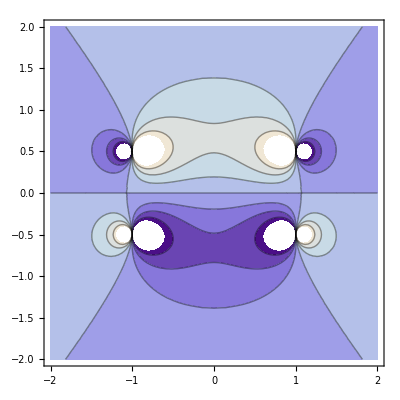
1. Combining, (∂_t +v·∇)B/ρ≡d/dt B/ρ=B/ρ·∇v; cf d/dt δl=v·∇δl. ρ(∂_t +v·∇) v + (∂_t +v·∇) (∂_t ρ + ∇·ρv)=∂_t ρv+∇·ρv⊗v
2.
s=1;BAH1=Bc[[3]]/.{y→0,z→-s/2+ζ};BAH2=Bc[[3]]/.{y→0,z→s/2+ζ};
ContourPlot[BAH1-BAH2,{x,-2,2},{ζ,-2,2}]
-Graphics-
3. Compose as three current squares. Dipoles associated with the top and the bottom squares cancel, leaving only the side square with dipole moment equal to 4 b^2 I .

## 5. Induction

### Reading

Z 462-7, 475-9, 486-91

### Electromagnetic Induction

#### EMF

M3⇒-Φ̇==EMF≡∮ds·E if circuit fixed in inertial frame. -Φ̇=∮ ds·(E+vxB), if circuit moves. Often a good idea to use differential form and work in inertial frame.
Faraday Disk: B parallel to Ω. In local inertial frame with v=Ωxr, E’=0, B'=B=O(v^2) ⇒V=-∫dr·vxB=-1/2Ω·BR^2

### Skin Effect

Suppose j=σE. and ignore charge and extermal current ⇒∇^2 X=μσ(∂X)/(∂t)+μϵ(∂^2 X)/(∂t^2); X=E,B. 
Diffusion equation with D=(μσ)^(-1/2)when L>(ϵ/μσ^2)^(1/2). Skin depth δ=(2/σωμ)^(1/2)for oscillatory signal. X~e^(-z/δ+i(z/δ-ωt)).  
J_0 for cylindtrical wire. 
Magnetic diffusion with same D  covered in wk4
Cu - σ=6 x10^7 Ω^-1 m^-1. ⇒D=0.013 m^2 s^-1⇒δ=0.013ω^(-1/2).

### Homework

Z 14.5, 14.16, 14.21. 
Weejee is working on a superconductivity problem which will be posted shortly.

## 6. Waves

### Reading

Null

### EM Waves in vacuo

#### Vector Potential and d’Alembertian

Basic Equations

A^α=[φ,A], F_αβ=A_(β,α)-A_(α,β); (A^α)_(,α)=0; (F^αβ)_(,β)=-(A^(α,β))_(,β)=μ_0 j^α; F_[αβ,γ]=0.
Hence ∇^2 φ-∂_tt φ≡□^2 φ=0; □^2 A=0. Now, E=-∇φ-∂_t A; B=∇xA ⇒ □^2 E=0, □^2 B=0.
Often convenient to write A=u(t,x)s. For monochromatic wave, (∇^2 +ω^2)u=0 (Helmholtz); use in optics.

#### Plane Waves

∝e^iϕ; ϕ=k·x-ωt; ω=±k; Coulomb is special choice of Lorenz, k·A=0; E=iωA;B=ikxA; E=B orthogonal and to k
General solutions E_+(z-t)+E_-(z+t) composed by Fourier integral
Superpose with different k; E=∫(d^3 k)/(2π)^3 E_k e^(i(k·x-ωt)) etc

Energy

U=ϵ_0 E^2=B^2/μ_0; S=U k̂; Z_0=μ_0 E/B=μ_0≡120π=377Ω- impedance of free space

### Polarization

#### Elliptical

Monochromatic wave has fixed polarization; rotate axes, shift phase E_x∝e^iϕ, E_y∝e^(i(ϕ+δ)); δ=0 linear, =±π/2, circular, elliptical in general.
LCP,RCP conventions are confused. LH ν has spin antiparallel to momentum  (unless overtake it) which is opposite convention from book!

```mathematica
ax=1.;ay=.5;
Animate[Graphics[{{Red,Arrow[{{0,0},{ax Cos[ϕ],ay Sin[ϕ]}}]},
                                {Green,  Arrow[{{0,0},{-ay Sin[ϕ],ax Cos[ϕ]}}]}},Axes->True,
AxesLabel->{Style["E_x",Red]Style["B_x",Green],Style["B_y",Green]Style["E_y",Red]}, PlotRange->{{-1,1},{-1,1}}],{ϕ,0,2π},AnimationRunning->False]
```

#### Stokes Parameters

Rotate polarization plane of linearly polarized monochromatic wave through ψ. E=E[cosψ,sinψ]cosϕ. I=ϵ_0 E^2 cos^2 ϕ, Q = ϵ_0(E_x^2-E_y^2)=Icos2ψ, U=2 ϵ_0 E_x E_y=Isin2ψ ⇒Q^2+U^2=I^2.
Set ψ=0 and add perpendicular oscillation in quadrature: E = [E_x cosϕ,E_y sinϕ]. I=ϵ_0(E_x^2 cos^2 ϕ+E_y^2 sin^2 ϕ), Q = ϵ_0(E_x^2 cos^2 ϕ-E_y^2 sin^2 ϕ),  V=2 ϵ_0 E_x E_ycosϕsinϕ ⇒Q^2+V^2=I^2
Combine on Poincaré Sphere: Q^2+U^2+V^2=I^2. For broad band wave with partial polarization, Q^2+U^2+V^2<I^2. 
Degree of linear polarization =((Q^2+U^2)^(1/2))/I; position angle : ψ=1/2 tan^-1 U/Q; degree of circular polarization=V/I. Note that adding π to ψ leaves the polarization unchanged, cf spinor!

#### Quarter - wave Plate

Two orthogonal modes of linear polarization with different n; eg calcite; thickness such that retard one mode by π/4. Incident linear at ψ=π/4 → circular and vice versa

### Waves in Uniform Media

Use D, H to get refractive index n=(μϵ)^(1/2), 
U=1/2 ϵE^2+1/2 μH^2, S=ExH =(U k̂)/n, Z=E/H=(μ/ϵ)^(1/2)

### Reflection, Refraction and Transmission

#### Boundary Conditions

D_⊥,B_⊥, E_(||),H_(||), k_(||), ω continuous at plane boundary.

#### Snell' s Law

k_(||)continuity ⇒nsinθ=const. for both reflected and transmitted waves;
Generalize to complex refractive index as with skin depth.

#### Normal Incidence

E_(||)→1+r=t, H_(||) →(1-r)/(Z_-)=t/(Z_+)⇒r=(Z_+-Z_-)/(Z_++Z_-); t=(2 Z_+)/(Z_++Z_-);⇒|r|^2 V_(g-)+|t|^2 V_(g+)=V_(g-). energy conservation
Generalize to complex n,Z,  oblique incidence, polarization, internal reflection, Brewster angle...

#### Fresnel Coefficients

Consider a “TM/TE” modes incident on a plane surface (z=0) with H/E along the y direction and E/H, k lying in the x-z plane.

```mathematica
Solve[{(1-r)Cos[SubMinus[θ]]==t Cos[SubPlus[θ]],(1+r)/SubMinus[Z]==t/SubPlus[Z]},{r,t}]
Solve[{1+r==t ,((1-r)Cos[SubMinus[θ]])/SubMinus[Z]==(t Cos[SubPlus[θ]])/SubPlus[Z]},{r,t}]
```

Equivalent expressions using refractive indices, permittivities can be derived; Z may be complex. These are used in designing single layer and multilayer coatings for Fabry-Perot devices and X-ray mirrors

### Strong Waves

Consider a single particle released from rest in a strong, monochromatic  electromagnetic wave, e.g. from a laser.
E=E(1,0,0)cosϕ, ϕ=ω(z-t), f=qE/mω, α=(γ-u_z)ω=-dϕ/dτ
m dγ/dτ= m du_z/dτ=qE_x u_x⇒α=const.
m du_x/dτ = (γ-u_z)E_x⇒du_x/dϕ=-fcosϕ⇒u_x=dx/dτ=-fsinϕ⇒x=-f/αcosϕ
u_z=dz/dτ= (ω^2 - α^2)/(2αω)+ ωu_x^2/(2α)=(ω^2 - α^2)/(2αω)+(f^2 ω)/(2α) sin^2 ϕ⇒z = ((α^2-ω^2)/(2 α^2 ω)-(f^2 ω)/(4 α^2))ϕ+(f^2 ω)/(8 α^2)sin2ϕ
γ=dt/dτ= (ω^2 + α^2)/(2αω)+ ωu_x^2/(2α)=(ω^2 + α^2)/(2αω)+(f^2 ω)/(2α) sin^2 ϕ⇒t = -((α^2+ω^2)/(2 α^2 ω)+(f^2 ω)/(4 α^2))ϕ+(f^2 ω)/(8 α^2)sin2ϕ
For a phase change -2π, t-z=(2π)/ω as it should.

```mathematica
f=100;α=(1+f^2/2)^(1/2);
ParametricPlot[{-f/α Cos[ϕ],(2 α^2-2-f^2)/(4 α^2)ϕ+f^2/(8 α^2)Sin[2ϕ]},{ϕ,0,-4π},Frame->True,FrameLabel->{x,y},RotateLabel->False]
```

### LCLS Undulators

LINAC Coherent Light Source (aka X-ray Laser) - accelerate electrons to 3-15 GeV (discuss later), wiggle transversely using undulator, radiate coherent X-rays, reflect into experimental hutches for spectroscopy, X-ray diffraction, high energy density physics etc...


-Graphics-

There are 33 undulators in a 132 m hall each undulator is 3.4 m long (leaving a 0.6m gap) and contains 113 pairs of pairs of permanent magnets of alternating polarity designed to give a sinusoidal perpendicular field B=B_0 sin kz where B_0=1.25T, k=(2π 113)/3.4=209 m^-1. 
Equivalently, the wavelength is 30 mm.
Here are two wavelengths ...NSNS...
                                              SNSN
The transverse equation of motion is dp_x/dt=evB so the deflection angle is θ= Δp_x/p=eB_0/mckγβ 
Conventional to define wiggler strength parameter K=γβθ=3.5. 
The undulating electrons will radiate and we will discuss this later.
Also have focusing magnets.
The X-rays are separated from the electron beam using grazing incidence X-ray mirrors.

### Metamaterials

Non-natural materials designed and fabricated to exhibit unusual electromagnetic properties
Important for GHz and THz  applications
Periodic structure < λ; effectively homogeneous

#### Negative Refractive Index

ENG (≡Epsilon NeGative?) materialshave ϵ_r<0; MNG have μ_r<0.
Can have metamaterials where ϵ, μ are both < 0. Using n(k̂)_(.08.08.08)xE=μH, nk̂xH=-ϵE, we find that n<0. E, H, k   have opposite handedness; V_ϕ antiparallel to S.; refract "backwards". Cerenkov properties!!
This, in turn, can be used to create a super lens which can beat the diffraction limit of angular resolution ~λ/D. The case n=-1 can create a “perfect lens” with point focus (in principle).
http://news.stanford.edu/pr/2013/pr-meta-material-invisible-050613.html
It can also be used to create an “invisibility cloak”(also in principle).
-Graphics-

#### Electromagnetic Induced Transparency

Consequence of Kramers-Kronig relations
-Graphics-

Narrow window of transparency when ϵ_r(blue) changes rapidly.
Can also slow the group velocity of light down to ~8m s^-1.
Local work in Harris, Vukevic groups.

### Galactic Center Magnetar

#### NuSTAR

Focusing hard (6-80 keV) X-ray telescope launched in June 2012; X-ray mirrors 10 m focal length, multilayers Pt/SiC, W/Si 200m coatings!
-Graphics-

#### Magnetar

http://www.astronomerstelegram.org/?read=5058
Pulsar ( neutron star moment of intertia I ~10^38kg m^2,B~16GT) with spin period P=3.76s slowing down at rate Ṗ=6.5x 10^-12 in 3Pm radius orbit around a 4 x 10^6 M_sun black hole. 
NuSTAR observed a massive flare radiating 10^33 J in a day; cf U_m ~ 4 πR^3 B^2/μ_0~10^39J;U_kin= 1/2 IΩ^2~ 10^38 J
The flare launched a low frequency magnetic wave into the surrounding plasma which behaves like a perfectly conducting magnetized medium described by MHD

#### Alfvén Waves

Consider simple wave modes in this medium.
In particular, a transverse wave propagating along B
Linearize:  ∂_t B_x=-∂_z (-u_xB)⇒ωB_x=-kBu_x, ∂_t ρ=0, ρ ∂_t u_x =j_y B = B/μ_0∂_z B_x⇒ρωu_x=-kB_x/μ_0B⇒ ω^2=k^2 B^2/(μ_0 ρ)=V_A^2 k^2, V_A is Alfvén speed
When k is oblique, ω=k·V_A, V_ϕ=V_A cosθ k, V_g=V_A.
Energy trasnported along field direction.
We can find additional modes if we add pressure.

#### Transverse Wave in Plasma (cf wk 3)

The pulsar also emits radio wave pulses at the spin frequency.
To describe their propagation, linearize the fluid equation for cold plasma - just consider the electrons and treat the ions as fixed
-iωn_e m_e v=-n_eeE ⇒ j= i(n_e e^2)/(m_e ω)E; imaginary conductivity
Combine with M3, 4⇒ ω^2=ω_p^2+c^2 k^2; where ω_p=((n_e e^2)/(m_e ϵ_0))^(1/2)=56(n_0/(1 m^-3))^(1/2)rad s^-1
The refractive index is therefore n=(1-ω_p^2/ω^2)^(1/2) and V_ϕ=c/n; V_g=nc.
This is also valid for free electrons in a metal.
The radio pulses travel at the group velocity and are subject to a dispersive delay t=(ω_p^2 L)/(2 ω^2 c) relative to light when traversing a distance L.
For the pulses from the new magnetar, the delay is measured to be t=6.8 ν_9^-2 s varying with the observing frequency ν_9 GHz. 
This is the largest dispersion delay ever measured.

Aside on Plasma oscillation

ω=ω_p. 
Add pressure - effective specific heat ratio is 3 because there is one degree of freedom.
Create waves when add electron pressure; dispersion relation: ω^2=ω_p^2+(3kT)/m k^2. Langmuir waves
Add ion inertia →ion acoustic waves.

#### Magnetic Field

Combine these two approaches to consider electromagnetic waves propagating in a cold electron plasma.
The equation of motion is: -i ω m_e v = -e(E+vxB_0), where B_0 is the background field along ẑ
while Maxwell’s equations give: kx(kxE)+ω^2 E+(i ω n_e e v)/(c^2 ϵ_0)=0,
Eliminate v to obtain an eigenequation M(ω,k)·E =0 which can be solved for the dispersion relations and eigenvectors.

```mathematica
vk=k{Sin[θ],0,Cos[θ]}/.θ->0;vE={Ex,Ey,Ez};
dv=Simplify[vE+ (vk×(vk×vE))/ω^2+(ⅈ  n e{vx,vy,vz})/(ϵ0 ω)/.Solve [{-ⅈ ω m vx==-e(Ex+vy B),-ⅈ ω m vy==-e(Ey-vx B),-ⅈ ω m vz==-e Ez},{vx,vy,vz}]/.{B->(-m ωg)/e, n->(m ϵ0 ωp^2)/e^2}][[1]];
dm=Simplify[Table[{dv[[i]]/.{Ex->1,Ey->0,Ez->0},dv[[i]]/.{Ex->0,Ey->1,Ez->0},dv[[i]]/.{Ex->0,Ey->0,Ez->1}},{i,1,3}]];
dr=Simplify[Eigensystem[dm]]
```

### Homework

1. Show that the parameters f, α associated with a strong, electromagnetic wave are Lorentz invariant. 
Hence show the energy contained in a wave packet transforms as the frequency and comment upon this.
Consider a particle released from rest in circularly polarized strong wave with f=1. Show a graph of z(t) for two periods of the wave.
2. Use the Fresnel coefficients derived above to confirm that when an unpolarized wave is incident from air on a plane glass (refractive index n~1.5) interface with θ_-=tan^-1 n), the reflected wave is completely polarized.
3. Z 17.11
4. In class, we considered the propagation of electromagnetic waves in an unmagnetized electron plasma. Now add a uniform field and consider waves propagating along it. Either working from first principles or using the code written above and correcting an error, show that there are two modes with refractive index n satisfying
n^2=1-ω_p^2/(ω(ω±ω_g)).
Describe the electric, magnetic and velocity vectors in these modes. 
There is actually a third mode. Explain its properties.
Repeat this exercise for waves propagating perpendicular to the field.
A linearly polarized wave with frequency ω >> ω_g propagates along the field. Estimate the angle through which the direction of the polarization will be rotated in traversing a distance L.
The propagation of the pulses from the magnetar can be approximated by assuming that it is parallel to a uniform field B_0=100pT.  Estimate the angle through which the plane of polarization has been rotated.

#### Answers

```mathematica
vk=k{Sin[θ],0,Cos[θ]}/.θ->0;
vE={Ex,Ey,Ez};
dv=Simplify[vE+ (vk×(vk×vE))/ω^2-(ⅈ  n e{vx,vy,vz})/(ϵ0 ω)/.Solve [{-ⅈ ω m vx==-e(Ex+vy B),-ⅈ ω m vy==-e(Ey-vx B),-ⅈ ω m vz==-e Ez},{vx,vy,vz}]/.{B->(-m ω Y)/e, n->(m ϵ0 ω^2 X)/e^2}][[1]];
dm=Simplify[Table[{dv[[i]]/.{Ex->1,Ey->0,Ez->0},dv[[i]]/.{Ex->0,Ey->1,Ez->0},dv[[i]]/.{Ex->0,Ey->0,Ez->1}},{i,1,3}]]
dr=Simplify[Eigensystem[dm]];
```

## 7. Transmission

### Reading

Z636-641, 667-8, 669-670, 677-682,704-705

### Transmission Lines

Conducting wires etc of constant cross section; seek TEM solutions ∝e^(i(kz-ωt)); medium may be susceptible; no longitudinal contribution to ∇.E, H so just a 2D problem. 
Boundary conditions on conductors.

#### Generalities

Vacuum

∇·B_⊥ = 0⇒∃Φ:B=[∂_y Φ,-∂_x Φ,0]e^(i(kz-ωt)); Φ(x,y) (a stream function) is the flux per unit line length as dy/dx=B_y/B_x⇒Φ const. on field lines; also A=(0,0,Φ)
M3⇒kxE=ω∇Φe^(i(kz-ωt)), ∇^2 Φ=0,  φ=ω/kΦ or more generally, ∂_t Φ=-∂_z φ; M4⇒kxB=ω^2/kc^2∇Φe^(i(kz-ωt)) ⇒ω=±ck, E=cB
Magnetic field lines are perpendicular to electric field (and both to axis) and are equipotentials and lie parallel to conductor surfaces; propagation along axis at c
On conductor surface, ∂_t σ+∇·J=0.

Medium

E=(μ/ϵ)^(1/2)H;ω=k/(μϵ)^(1/2)

#### Coax

Cylindrical symmetry H_ϕ=(ϵ/μ)^(1/2)E_r=I/(2πr); L=μ/(2π)ln(b/a) per unit length ∂_z V=-L∂_t I
Likewise, Q=2πrE per unit length or Q=CV, C=(2πϵ)/(ln(b/a))⇒∂_t Q = C ∂_t V=-∂_z I ⇒ ∂_zz V=LC∂_tt V, ∂_zz I=LC∂_tt I, Telegraphers’ Equations
Follows from circuit analysis; add more capacitative and inductive units in series, parallel; add resistance ∂_z V=-IR-L∂_t I etc

#### Parallel wires

Illustrate use of complex variables for 2D electrostatics (traditionally large part of subject, also hydro!)
In 2D φ =-q/(2πϵ)ln(r)=-q/(2πϵ)Re[lnz]
In general f(z)=u+iv satisfies CR ⇒u,v harmonic in 2D.
For two line charges, φ~ln((z+1)/(z-1))

```mathematica
φ=Log[(√((1+x)^2+y^2))/(√((1-x)^2+y^2))];vE=Simplify[-{D[φ, x],D[φ, y]}];vH=Simplify[-{-D[φ, y],D[φ, x]}];
plt1=Show[StreamDensityPlot[{vE,φ},{x,-2,2},{y,-2,2},ColorFunction->Hue],Graphics[{PointSize[Medium],Point[{{-1,0},{1,0}}]}]];
plt2=Show[StreamDensityPlot[{vH,φ},{x,-2,2},{y,-2,2},ColorFunction->Hue],Graphics[{PointSize[Medium],Point[{{-1,0},{1,0}}]}]];
GraphicsRow[{plt1,plt2},ImageSize->500]
```

### Waveguides

#### Heuristic treatment

Wireless transmission by reflection at conducting surface TEM cannot satisfy BC wo interior current, ∇xH.
Consider oblique EM plane wave modes w k_⊥^2=μϵω^2-k^2 combine a Fourier sum over ϕ of standing modes with k_⊥=k_⊥(cosϕ,sinϕ) so as to satisfy BC
(∂_xx +∂_yy +k_⊥^2)H_z,E_z=0 for TE,TM; can only do this for special values of k_⊥- eigenvalues with orthogonal eigenfunctions; generally fix ω, solve for k; will be cut off frequencies
BC E_(||)=0. TE: E_z=0 plus component ∇xH parallel to surface and perpendicular to axis must vanish ⇒ (n·∇)H_z=0 from M4; TM: E_z=0 suffices as (∇xE)_z=0 
Mathematically solve scalar Helmholtz+ Dirichlet, Neuman in 2D in given geometry; cf QM energy levels
Formal proofs in Z.

#### Modes

Plot dispersion relation ω(k) for given mode, will be cut off ω where k=0,  and below which only evanescent propagation is possible; specifically ω_c=(μϵ)^(-1/2)k_⊥
Just like unmagnetized plasma! same algebra!; V_g V_ϕ=(ϵμ)^(-1/2)  P=Uv_g etc

#### Rectangular Waveguide

cf particle in box k_(⊥mn)=(π(m^2/a^2+n^2/b^2))^(1/2).
TE_(10,01)TM_11 are lowest  modes

```mathematica
-Graphics--Graphics-
```

#### Circular etc waveguides

Bessel functions... In practice have complex cross section and handle numerically

#### Varying cross sections

If change slowly handle using (J) WKB approximation; avoid reflection
If change abruptly, eg open/closed end, get reflections; impedance conditions

### Cavities

Completely closed conducting surfaces have resonant eigenfrequencies and can be used to detect weak signals eg axion search; Tesla fields exclude axions ~2-4 μeV.

### Microwave Background Telescopes

#### Polarization

Much effort now being expended to see signatures of inflation in the microwave background radiation polarization maps. Later.
-Graphics-
e.g. QUaD (Church) and BICEP (Kuo) experiments; QUaD was a 2.6m telescope in a ground shield
New experiments under design
-Graphics-
-Graphics-
The radio waves are reflected into 31 feed horns, pass though circular waveguides and are measured using 5 mm bolometers. 
The waveguide is a high pass filter with cutoff ν>75 GHz, λ<4mm.
Copper meshes and the atmosphere act as low pass filter allowing a small bandwidth to be measured.

#### TE_11 Cylindrical waveguide

Choose this mode as it looks like a plane polarized EM wave
Helmholtz: (∇^2 +k_⊥^2)H_z=(∂_rr +1/r∂_r +1/r^2∂_ϕϕ +k_⊥^2)H_z=0⇒H_z∝J_1(k_⊥r)cosϕ
BC: ∂_r H_z=0 at r=R; first zero of J_1' =(J_0-J_2)/2 is 1.84 ⇒ k_⊥=(2 π)/(4mm)=1.57 x10^3 m^-1 ⇒R=1.84/1.57=1.2mm
Transverse fields: ∇.B=0⇒ikH_z+∂_x H_x+∂_y H_y=0 ⇒ik∂_x H_z+∂_xx H_x+∂_xy H_y=0; E_z=0 ⇒ik∂_x H_z+∂_xx H_x+∂_yy H_x=0; 
Helmholtz ⇒H_⊥ = i k/(k_⊥^2) ∇_⊥ H_z; M3⇒E=μω/kHxẑ

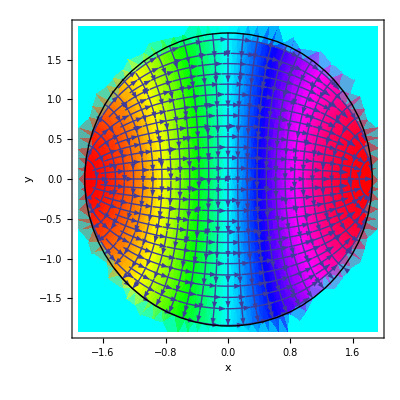

```mathematica
R=r/.FindRoot[BesselJ[0,r]-BesselJ[2,r]==0,{r,1.8}];
Hz=If[r<R,BesselJ[1,r]Cos[ϕ],0]/.{r->(x^2+y^2)^(1/2),ϕ->ArcTan[x,y]};
vH={D[Hz, x],D[Hz, y]};vE={vH[[2]],-vH[[1]]};
Show[StreamDensityPlot[{vH,Hz},{x,-R,R},{y,-R,R},FrameLabel->{x,y},RotateLabel->False,ColorFunction->Hue],StreamPlot[vE,{x,-R,R},{y,-R,R}],Graphics[{Thick,Circle[{0,0},R]}]]
```

#### Feed Horn

Arrange impedance at entrance so that Z=E/H=Z_0, matched to incoming vacuum wave.

### SLAC LINAC

#### History

3km e^+/e^- linear accelerator; waveguide operating in TM mode→E_z 
Excited by a series of klystrons - powerful microwave transmitters using up to 50 MW! (invented by Hansen, Varians!) 
Historically, beams separated into: 
SLC(50+50 GeV for 90 GeV Z physics) storage ring; ⇒E_z~17V m^-1; 
PEP-II (9+3 GeV for 5 GeV B physics)
LCLS (5-15 GeV) LCLS; just need 1km
Future linear accelerators planned for ~0.5TeV, ~ 30 Vm^-1

#### Operation

V_(`ϕ)>c ⇒ particles accelerated and decelerated; pre-acceleration has decelerating fields shielded in drift stage
transit time ~10μs ⇒ electron trails light by only ~E_GeV^-2μ!; use periodic array of Cu irises to create V_ϕ=c
-Graphics-
Bloch theorem ⇒ E_z(0, 0)∝e^ikz∑c_n e^inκz wh κ=(2π)/(26 mm); need large c_n for ω=c(k+nκ) ~ GHz.

### Fiber Optics

#### e.g. LSST

8.4m (6.5m effective) mirror telescope being built in Chile, 10 sq deg FOV covering half sky a thousand times over 10 years.  
Prime purpose is to monitor expansion of the universe. 
SLAC leading building the camera; 3 Gpx image every 15s.
Need to communicate alerts globally in 2s; 15 TB per day on a 10 Gbps fiber down mountain.
-Graphics-

#### Step Index Mode

This is geometrical optics with total internal reflection; minimize losses;  n decreases outward; (2 x πa^2 x πk_⊥^2)/(2π)^2 =(a^2 k^2)/2(1-n_1^2/n_2^2)^2modes.
In practice concerned about evanescent modes and diffractive effects.

#### Graded Index Mode

Rays obey differential equation: d/ds n dx/ds=∇n which can be derived from Fermat’s principle

#### Physical Optics Mode

Solve full wave optics problem with boundary conditions

### Homework

1. Consider a cylindrical waveguide of radius R operating in TM_32 mode in vacuo.
Adapt the treatment above for a TE_11 mode explaining the differences and relating to the boundary conditions to exhibit an image of the transverse electric and magnetic modes.
Find the cutoff frequency if R=10mm. 
2. A self-focussing graded optical fiber has a refractive index n(r)=(n_0(1-α^2 r^2))^(1/2). Working from the Helmholtz equation or otherwise, seek an axisymmetric mode with Gaussian radial profile that propagates along the fiber without spreading.
What are the phase and group velocities for this mode?
3. Z19.23

#### Sketch Solutions

1.

TM_32:H_z=0, E_z satisfies Helmholtz (∂_rr +1/r∂_r +1/r^2∂_ϕϕ +k_⊥^2)E_z=0 with E_z=0 at r=R. 
⇒E_z=J_3(r)cos3ϕ; R is 2nd zero of J_1;
∇·E=0 ⇒ikE_z+∂_x E_x+∂_y E_y=0 ⇒ik ∂_x E_z+∂_xx E_x+∂_xy E_y=ik ∂_x E_z+∂_xx E_x+∂_yy E_x=0

```mathematica
R=N[BesselJZero[3,2]]
Ez=If[r<R,BesselJ[1,r]Sin[3ϕ],1]/.{r->(x^2+y^2)^(1/2),ϕ->ArcTan[x,y]};
vE={D[Ez, x],D[Ez, y]};vH={vE[[2]],-vE[[1]]};
Show[StreamDensityPlot[{vE,Ez},{x,-R,R},{y,-R,R},FrameLabel->{x,y},RotateLabel->False,ColorFunction->Hue],StreamPlot[vH,{x,-R,R},{y,-R,R}],Graphics[{Thick,Circle[{0,0},R]}]]
```

k_⊥ = 9.76/(.01)= 980 m^-1; ν_min=(3x 10^8 x 980)/(2π)=47GHz

2.

(∂_rr +1/r∂_r +(n^2 ω^2)/c^2-k^2)ψ=(∂_rr +1/r∂_r +(n_0^2 ω^2(1-α^2 r^2))/c^2-k^2)ψ=0; satisfy BC with internal reflection if ψ is E_ϕ
Let ψ=e^(-β^2 r^2+ikz-ωt); (αn_0 ω)/c=2 β^2; (n_0^2 ω^2)/c^2-k^2= 4 β^2=(2 αn_0 ω)/c; ω/k=c/n_0(α/k+(1+α^2/k^2)^(1/2)); dω/dk=c/n_0(1 + α^2/k^2)^(-1/2)

```mathematica
ψ=ⅇ^(-β^2 r^2);Simplify[ψ^-1(D[ψ, r,r]+r^-1 D[ψ, r]+ω^2(1-α^2 r^2)ψ-k^2 ψ)]
```

3.

E_z=sinπx sinπye^-iωt; ω=2^(1/2)π; B=-2^(-1/2)i[sin πxcosπy,cosπxsinπy,0]e^-iωt
Poynting flux time-averages to zero; <T_xx> only from B_y^2/(2 μ_0)  pressure which averages to a force <F_x>=ah/(16 μ_0); likewise for <F_y>; no net force on ends because averaged electric tension cancels averaged magnetic pressure.

## 8. Radiation

### Reading

Z 730-739, 752-760, 762-765, 775-780, 787-789

### Relativistic radiation

#### Lie'nard - Wiechert Potential

Wk2,4: ∇^2 φ=-ρ/ϵ_0⇒φ=1/(4 πϵ_0)∫d^3 x(ρ(x))/R ,∇^2 A=-μ_0j⇒A(r)=μ_0/(4π)∫d^3 x(j(x))/R; where r-x=Rn;
Hence, □A=-μ_0j ⇒ A=-μ_0/(4π)∫d^3 x(γ j)/(ξ·u), where ξ=r-x=R(1,n) is the null separation 4-vector from the Source at x=[s,x] to the Observer at r=[t,r]; nb k_α^O dr^α=k_α^S dx^α.
For a single charge, A=-(μ_0 q u)/(4π ξ·u), which is manifestly covariant; nb u =dx/dτ=[(1+u·u)^(1/2),u]=γ(1,⋁)
We will also use A=μ_0/(4π)∫dsd^3 x j/(R(1-n·β))δ(s+R-t)|(d(s+R-t))/ds| =μ_0/(4π)∫d^4 x j/Rδ(s+R-t)

#### Field Tensor

ξ must remains null as x(τ) varies; consider r(τ); ξ·(dr/dτ-u)=0⇒ξ_β dr^β/dτ∂_α τ=ξ_β u^β∂_α τ ⇒ ∂_α τ=ξ_α/(ξ·u); nb derivatives wrt observer coordinate r^αand u evaluated at source.
Now ∂_α (ξ·u)=ξ_β∂_α u^β+u_β∂_α ξ^β=(ξ_α ξ_β a^β)/(u^β ξ_β)+u_β((δ^β)_α-u^β∂_α τ) =((1+ξ·a)ξ_α)/(ξ·u)+u_α, where a^α=du^α/dτ =[a·v,a] is the acceleration, orthogonal to u 
Hence  A_(α,β)= ((μ_0 q)/(4 (π(ξ_γ u^γ))^2)) (u_α∂_β (ξ_δ u^δ)-∂_β u_α ξ_δ u^δ) =  ((μ_0 q)/(4π ξ·u^2))(u_α u_β-a_α ξ_β-(u_α ξ_β)/(ξ·u)(1+ξ·a)); note that ∂_α A^α=0 as it must. Now, F_αβ=∂_α A_β-∂_β A_α
Finally, F=((μ_o q)/(4πξ·u^3))[(1+ξ·a)(ξ⊗u-u⊗ξ)-ξ·u(ξ⊗a-a⊗ξ)]

```mathematica
ξ={ξ0,ξ1,ξ2,ξ3};u4={u0,u1,u2,u3};a4={a0,a1,a2,a3};η={{-1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}};
ip[a_,b_]:=a.η.b;op[a_,b_]:=Outer[Times,a,b]
fuu=1/(4π ip[ξ,u4]^3)Simplify[(Outer[Times,a4,ξ]-Outer[Times,ξ,a4])ip[ξ,u4]+(Outer[Times,ξ,u4]-Outer[Times,u4,ξ])(1+ip[ξ,a4])]
fdd=η.fuu.η
```

#### Electromagnetic Field

E_i= F_i0, B_i=ϵ_ijk F^jk; 
E=(μ_0 q)/(4π)[((1-v^2)(n-v))/((1-n·v)^3 R^2)+(n×{(n-v)×v̇})/((1-n·v)^3 R)]; B=(μ_0 q)/(4π)n×[-((1-v^2)v)/((1-n·v)^3 R^2)+(n×(v×v̇}-v̇)/((1-n·v)^3 R)]=n×E

```mathematica
e1=Simplify[fuu[[1,2]]/.{ξ0->R,ξ1->R n1,ξ2->R n2,ξ3->R n3,u0->γ,u1->γ v1,u2->γ v2,u3->γ v3,a0->γ^4 vw,a1->γ^4 vw β1 +γ^2 w1,a2->γ^4 vw v2 +γ^2 w2,a3->γ^4 vw v3 +γ^2 w3}];
1/R^2 Simplify[Coefficient [e1,R^-2]/.n1 β1+n2 v2+n3 v3->nv]+1/R Simplify[Coefficient [e1,R^-1]/.n1 v1+n2 v2+n3 v3->nv]
b1=Simplify[fuu[[3,4]]/.{ξ0->R,ξ1->R n1,ξ2->R n2,ξ3->R n3,u0->γ,u1->γ v1,u2->γ v2,u3->γ v3,a0->γ^4 vw,a1->γ^4 vw β1 +γ^2 w1,a2->γ^4 vw β2 +γ^2 w2,a3->γ^4 vw β3 +γ^2 w3}];
1/R^2 Simplify[Coefficient [b1,R^-2]/.n1 v1+n2 v2+n3 v3->nv]+1/R Simplify[Coefficient [b1,R^-1]/.n1 v1+n2 v2+n3 v3->nv]
```

#### Invariants

-(F^αβ F_αβ)/2 =E^2 - B^2 =((μ_0 q)/(4π ξ·u^3))^2[((1+ξ·a)u-ξ·u (a)·ξ])^2=((μ_0 q)/(4π ξ·u^2))^2,(F^αβ ϵ_αβγδ F^γδ)/8=E.B=0

### Stress-Energy Tensor

T_em=(U | S
g | T_M); T^αβ=1/μ_0(1/4 F_γδ F^δγ η^αβ -(F^α)_γ F^γβ)⇒T=(μ_0 q^2)/(16 π^2 ξ·u^6)[(a·a ξ·u^2-(1+ξ·a)^2)ξ⊗ξ-(1+ξ·a)ξ·u(ξ⊗u+u⊗ξ)+ξ·u^2(ξ⊗a+a⊗ξ+1/2 η)]
We can decompose this into three parts:
T_near=(μ_0 q^2)/(16 π^2 ξ·u^6)[-ξ⊗ξ-ξ·u(ξ⊗u+u⊗ξ)+1/2 ξ·u^2η]
T_int=(μ_0 q^2)/(16 π^2 ξ·u^6)[-2ξ·a ξ⊗ξ-ξ·u ξ·a (ξ⊗u+u⊗ξ)+ξ·u^2(ξ⊗a+a⊗ξ)]
T_far=(μ_0 q^2)/(16 π^2 ξ·u^6)[(a·a ξ·u^2-ξ·a^2)ξ⊗ξ]
Can verify that ∂_β T^αβ=0; in fact ∂_β T_far^αβ=0

### Power and Radiation Reaction

#### Emitted Power

ξ·dξ=0, dr=0 ⇒  dt=ds(1-n·v)
S_far^r=T_far^(0r)=(μ_0 q^2 R^2)/(16 π^2)((a·a)/(ξ·u^4)-(ξ·a^2)/(ξ.u^6))n
P_em=∫dΩR^2 dt/ds S_far^r=∫dΩR^2(1-n·v)S_far^r=(μ_0 q^2)/(4π)(a.a-(a.a-a·v^2)/3)=(μ_0 q^2 a·a)/(6π)using a=[a.v,a].
(The integrals are elementary and even simpler if we recognize that the power is a Lorentz invariant and therefore can only be a function of a·a.)
P_em=(μ_0 q^2 γ^6((v̇)^2-vx(v̇)^2))/(6π)in terms of three velocity, acceleration
P_em=(μ_0 q^4 u.F.F.u)/(6 πm^2)in terms of field
P_em=(μ_0 q^2 a·a)/(6π), if v⊥a; =(μ_0 q^2 a·a)/(6 πγ^2), if v||a

```mathematica
Integrate[2π Sin[θ](1-v Cos[θ])^-3,{θ,0,π},Assumptions->0<v<1];
Integrate[Sin[θ](Cos[θ]Cos[ψ]+Sin[θ]Sin[ψ]Cos[ϕ]-v Cos[ψ])^2/(1-v Cos[θ])^5,{θ,0,π},{ϕ,0,2π},Assumptions->0<v<1];
```

#### Radiation Reaction

For an electron at rest with constant a, there can be no 3-momentum radiated. Therefore dp=-P_emdx is satisfied and so P_emis a Lorentz invariant. (nb in a general frame, dp/ds= -P_emv)
This argument breaks down if a changes ⇒ dp=-(μ_0 q^2(a·a dx+Kda))/(6π) and K=-1 (see HW); introduce the 4-jerk j≡da/dτ;  resistive (or radiation reaction) 4-force is f_res = dp/dτ= -(μ_0 q^2)/(6π)(a·au-j) ⇒ P_res = (dp/ds)_res·v=P_em+(μ_0 q^2)/(6π)j^0/γ
If return to the same a (including zero) no extra energy radiated; temporary storage in near/int fields.

### Examples

#### Uniform Motion

From LW

ξ·u = -γR (1 - n·v) = γr·n = -(γ(r^2 - rxn^2))^(1/2)=-γ (r(1-v^2 sin^2 θ))^(1/2)⇒ A=(μ_0 qu)/(4πγ (r(1-v^2 sin^2 θ))^(1/2)), F=(μ_0 q)/(4 πγ^3(r^3(1-v^2 sin^2 θ))^(3/2))(ξ⊗u-u⊗ξ) 
So E=(μ_0 q)/(4 πγ^3(r^3(1-v^2 sin^2 θ))^(3/2))γR(n-β) =(μ_0 q r)/(4 πγ^2(r^3(1-v^2 sin^2 θ))^(3/2))away from contemporary position of source; B=vxE

From Lorentz Transformation

Agrees as: E_(||)=E'_(||); E_⊥=γE'_⊥=(μ_0 γ q)/(4π(x'^2+y^2)); B_⊥=βxE; field lines bunch in transverse direction,

```mathematica
v=.9;c=.1;vE={(x(1-v^2))/((x^2+y^2-v^2 y^2+c^2)^(3/2)),(y(1-v^2))/((x^2+y^2-v^2 y^2+c^2)^(3/2))};
VectorPlot[vE,{x,-1,1},{y,-1,1}]
```

#### Non-relativistic, Electric Dipole Radiation

In far field, S^r=(μ_0 q^2 axn^2)/(16 π^2 R^2)= (μ_0(p^(..))_⊥^(.082))/(16 π^2 R^2)=E^2/μ_0⇒ E=((p^(..))_⊥)/(4 πϵ_0 R) with electric vector (polarization) evaluated at retarded time along projected dipole direction (Larmor).
More generally, (p^(..))_⊥→∫dV∂_t j_⊥
When j not harmonic, expand as ∫dω/(2π)e^-iωt j̃(ω)

#### Movie

For a single charge with v<<1, E = ((μ_0 q)/(4π)[n/R^2+ (n×(n×v̇))/R])_ret ; the first term is the Coulomb field, the second the far field
For a pure dipole comprising two opposite charges oscillating in antiphase, E = (μ_0/(4π)[(3(p·n)n)/R^3-p/R^3+ (n×(n×p^(..)))/R])_ret=(μ_0/(4π)[(3(p·n)n)/R^3-p/R^3+ (ω^2 p_⊥)/R])_ret

```mathematica
Animate[StreamPlot[{(3x y)/((x^2+y^2)^(5/2))-(x y)/((x^2+y^2)^(3/2)),(2 y^2-x^2)/((x^2+y^2)^(5/2))+x^2/((x^2+y^2)^(3/2))}Cos[t-(x^2+y^2)^(1/2)],{x,.1,4π},{y,-2π,2π}],{t,0,2π}]
```

#### Thomson scattering:

Free electron, photon energy <<m, f=eE/mcω<<1
a=-eE/m; σ_T= P_em/(ϵ_0 E^2)=(8π)/3 r_e^2=6.7 x10^-28 m^2; r_e =2.8fm; dσ/dΩ=(r_e^2(e_i·e_o))^2=σ_T/2(1+cos^2 θ), if average over incident polarization and sum over scattered polarization

#### Microwave Background Polarization

Density inhomogeneity at recombination can lead to polarization. Sky pattern is E-mode. Complementary pattern is B-mode which can be produced by gravitational lensing but which may be a gravitational radiation relic of inflation. Need nK sensitivity!

```mathematica
-Graphics--Graphics--Graphics-
```

#### Magnetic Dipole and Electric Quadrupole Radiation (outline)

When p^(..)=0, j→j+n·r'∂_t j+...→j+1/2∂_t ((r'xj)xn+(r'·nj+n.jr'))
First (antisymmetric part) → magnetic dipole radiation; second (symmetric part)→electric quadrupole radiation 
Now m=1/2∫dVr'xj; B_far = -(μ_0(m^(..))_⊥)/(4πr); P_em=(μ_0(m^(..))_⊥^2)/(6π)
Likewise, EQ radiation P_em=(μ_0 Q^(..):Q^(..))/(180π)in the notation of wk2 (different from Z)

#### Pulsars

Spinning, magnetized neutron stars (a perfect electrical conductor with M~ 3 x 10^30 kg, R~10 km) and surface magnetic flux density B_s.
- Crab pulsar B_s~100MT Ω~200 rad s^-1.
- Millisecond pulsar B_s~100 kT, Ω~3000 rad s^-1
- Magnetars B_s~30 GT, Ω~2 rad s^-1.
Originally modeled as vacuum magnetic dipole with P_em~(Ω^4 B_s^2 R^6)/(6 π μ_0)
We now know that this model is wrong because it leads to a magnetosphere with strong electric field which would quickly fill up with plasma.

#### Klystrons

The Klystrons in the SLAC LINAC contain a beam of ~100 keV electrons that is bunched by an electromagnetic wave and then enters a resonant cavity with frequency ~3GHz. This excites an electromagnetic wave which is ported out through a rectangular waveguide where it accelerates the beam with an electric field ~ 17MV m^-1The klystrons are arranged along the beam and phased so that the pulses of electrons see the peak accelerating electric field throughout their passage down the LINAC. 
-Graphics-

### Homework

1. Work through the  treatment of magnetic dipole radiation in Z 20.7.2 and show that a permanent magnetic dipole oriented  perpendicular to the axis about which it spins with angular frequency Ω radiates a power of order P_em~(Ω^4 B_s^2 R^6)/(6 π μ_0) where R is the radius of the star and B_s is the magnetic flux density at the stellar surface. (c=1 throughout.) 
a) Evaluate this for the three types of pulsar described above. 
b) Compute or sketch the magnetic field in the equatorial plane and contrast with the electromagnetic field radiated by a spinning electric dipole.
c) In a real pulsar the electric field surrounding the neutron star is so strong that plasma can be drawn from the surface and short out the component of electric field parallel to the magnetic field. Show that the electric charge density is ρ ~ ΩB/μ_0  and explain why the estimate of P_emabove remains valid.
d) The electromagnetic field also carries away angular momentum. Explain why the total torque must equal Ω^-1 P_em
e) A spinning magnetized neutron star can also radiate linear momentum. Explain how this can happen. Hint: consider what might happen if there is magnetic quadrupole as well as a magnetic dipole.
2. Z 20.10
3. We argued in class that the resistive force acting on an emitting electron involves the 4-jerk j=da/dτ. 
a) Show that j^α=[v·j+(1-v^2)^(1/2)(a.a-(a·v)^2), j]
b) Explain why if f_res=dp/dτ=-(μ_0 q^2)/(6π)(a.a u+Kj), then K=-1 
c) Re-express this in the form f_res=(μ_0 q^2)/(6π)(j.u u+j)

#### Sketch Solutions

1.

By analogy with Larmor formula P~μ_0/(6π)(m^(..))^2~μ_0/(6π)( (4 πΩ^2 BR^3)/μ_0)^2[Apologies for misprint in question]
a) P~(8 πΩ^4 B^2 R^6)/(3 μ_0 c^3)~ 200 Ω^4 B^2 kW ~3 x 10^31 W (Crab), ~ 10^30W (millisecond), ~ 3 x 10^28W (magnetar)
b) Trailing spiral B_ϕ alternating with radial wavelength (2π)/Ω in contrast with electric dipole radiation where we have E_ϕ
c) E ~ΩrB⇒ρ~(ϵ_0 E)/r; dimensional analysis or observe that transition from near to far field where r~Ω^-1 ; B~(B_s(R/r))^3 and P~B^2/μ_0 r^2
d) Torque G on star does work at the rate GΩ which must equal P to conserve energy.
e) When evaluating the Poynting flux, the cross term involving the dipole and quadrupole can interfere constructively in one hemisphere and destructively in the other giveing a net radiation of linear momentum

2.

a) P_Ω=(μ_0 I_0^2)/(8 π^2)(((coskdcosθ - coskd)/sinθ))^2 ~(μ_0(I_0^2(kd))^4 sin^2 θ)/(32 π^2)
b) p = i/ω ∫dzI =(2 iI_0)/k^2(1-coskd)~iI_0 d^2 etc
c) I(0)~i_0kd ⇒ p=(2iI(0)d)/ωetc

3.

a) u·u = -1 ⇒ u.a = 0 ⇒ a^0 = a·v; a·a + u.j = 0 ⇒ (a·v)^2 - a.a+γj^0-γv·j=0
b) u·dp/dτ=0 ⇒Kj·u=a·a ⇒K=-1
c) f_res=(μ_0 q^2)/(6π)(j-a·au)=(μ_0 q^2)/(6π)(j·uu+j)

## 9. Relativity

### Reading

Z 797-806, 891-898, 906-909

### Synchrotron Radiation

#### Far Field

A = -(μ_0 q u)/(4π u·ξ)⇒A=(μ_0 q v)/(4πR(1-n·v))and Ã=∫dte^iωtA=(μ_0 q)/(4πR)∫dxe^iωt, using dt=ds(1-n·v).
OverTilde[B_far]=ikx Ã⇒OverTilde[E_far]=iωnx(Ã xn)=iω(Ã)_⊥

#### Gyro radiation

Particle travels in a circle of radius κ^-1 with speed v and Ω=κv, observer at distance R with latitude θ
When v<<1, radiation at gyro frequency; spectrum is a δ-function; 
When v~1, get contributions from harmonics - a Fourier series. 
E=∑E_n e^inΩt, E_n=(μ_0 q Ω)/(8 π^2 R)∫_0^((2π)/Ω) ds e^(iω(s-n·x))v_⊥, v_⊥=v[cos Ωs, sinΩs sinθ], r.n=v/Ω cosΩs cosθ ⇒E_n~ J_n(nvcosθ) and similar terms 
If there is dispersion in v, harmonics overlap; treat spectrum as continuous.

#### Ultrarelativistic Limit

Power

P_em=(μ_0 q^2)/(6π)a·a =(μ_0 q^2)/(6π)γ^4 κ^2, for perpendicular acceleration with κ the curvature.

Fourier Transform

Ignoring constant phase factor, Ẽ=(μ_0 q ω)/(4πR)∫ds e^(iω(s-n·x))v_⊥=(μ_0 q ω)/(4πR)∫ds e^(i ωs/2(γ^-2+θ^2+κ^2 s^2/3))[κ s,θ], to lowest order, where θ is the observer inclination from the osculating plane, κ is the curvature at mid-point, the polarization is relative to axes parallel and perpendicular to the curvature direction, using n·x=(sinκvs cosθ)/κ and expanding
The limits of integration can be set as ±∞ and the integral converges.

```mathematica
Plot[Cos[(3ξ x)/2(1+x^2/2)]/.ξ->1,{x,0,10}]
NIntegrate[Cos[(3ξ x)/2(1+x^2/2)]/.ξ->2,{x,0,100}]
```

We convert to standard integrals using s→(2(1+γ^2 θ^2)^(1/2))/(κ γ)sinhy/3, ω_c=3 γ^3 κ, x=ω/ω_c; (also expressible as Airy functions - solution of y’’=xy); nb ω_c agrees with J and twice that in Z)

```mathematica
Simplify[ (μ0 q ω)/(4π R){ ⅈ κ s Sin[ω/2 (((1+γ^2 θ^2) s)/γ^2+(κ^2 s^3)/3)],θ Cos[ω/2 (((1+γ^2 θ^2) s)/γ^2+(κ^2 s^3)/3)]}D[((2(1+γ^2 θ^2)^(1/2))/(κ γ)Sinh[y/3]), y]/.{s->(2(1+γ^2 θ^2)^(1/2))/(κ γ) Sinh[y/3],ω->3 γ^3 κ x}]
```

Hence, Ẽ=(μ_0 q x (γ(1 + γ^2 θ^2))^(1/2))/πR{i(1 + γ^2 θ^2)^(1/2) ∫_0^∞ dysin[(x(1+γ^2 θ^2))^(3/2)sinhy].08sinh((2 y)/3),γθ ∫_0^∞ dycos[x (1+γ^2 θ^2)^(3/2)sinhy].08cosh(y/3)}
                 =(3^(1/2) μ_0 q x (γ(1 + γ^2 θ^2))^(1/2))/(2πR) {(i(1 + γ^2 θ^2))^(1/2)K_(2/3)((x(1+γ^2 θ^2))^(3/2)),γθ K_(1/3)((x(1+γ^2 θ^2))^(3/2))}

```mathematica
x=1;θm=2;Plot[{(1+θ^2)x BesselK[2/3,x(1+θ^2)^(3/2)],θ (1+θ^2)^(1/2)x BesselK[1/3,x(1+θ^2)^(3/2)]},{θ,-θm,θm}, Frame->True,FrameLabel->{"θγ","Ẽ",x,""},RotateLabel->False]
```

Fluence

Parseval -> ∫_(-∞)^∞ dt E^2/μ_0= 1/R^2∫_0^∞ dωI_ωΩ, where I_ωΩ=(|Ẽ|^2 R^2)/πμ_0=(3 μ_0 q^2 x^2 γ^2(1+γ^2 θ^2))/(4 π^3){(1+γ^2 θ^2) K_(2/3)^2((x(1+γ^2 θ^2))^(3/2))+γ^2 θ^2 K_(1/3)^2((x(1+γ^2 θ^2))^(3/2))}

Angular Distribution

I_Ω= ∫dω I_ωΩ=(3 μ_0 q^2 γ^5 κ)/(4 π^3(1 + γ^2 θ^2)^(7/2)))((1+γ^2 θ^2)∫_0^∞ dξξ^2 K_(2/3)^2(ξ)+γ^2 θ^2∫_0^∞ dξξ^2 K_(1/3)^2(ξ))=(μ_0 q^2 γ^5 κ)/(64(π(1 + γ^2 θ^2))^(7/2))(7(1+γ^2 θ^2)+5 γ^2 θ^2)

```mathematica
Integrate[ξ^2 BesselK[ν,ξ]^2,{ξ,0,∞},Assumptions->1/3<ν<2/3]
```

nb no 1-n·v factor unless charge moves closer to observer over averaging interval.

```mathematica
Plot[(1+θ^2)^(-5/2)+θ^2(1+θ^2)^(-7/2),{θ,0,3},Frame->True,FrameLabel->{"γθ","I_Ω"},RotateLabel->False]
```

Power Check

P=κ∫_(-∞)^∞ dθ I_Ω=(μ_0 q^2 γ^4 κ^2)/(64π)(7∫_(-∞)^∞ dx/((1 + x^2)^(5/2))+5∫_∞^∞ dxx^2/((1 + x^2)^(7/2)))=(μ_0 q^2 γ^4 κ^2)/(6π)

```mathematica
Integrate[7/((1+x^2)^(5/2))+(5 x^2)/((1+x^2)^(7/2)),{x,-∞,∞}]
```

Spectral Power

P_ω=κ∫_(-∞)^∞ dθ I_ωΩ=(3 μ_0 x^2 q^2 γ^2 κ^2)/(4 π^3)(∫_(-∞)^∞ (dθ(1+γ^2 θ^2))^2 K_(2/3)^2((x(1+γ^2 θ^2))^(3/2))+∫_(-∞)^∞ dθ γ^2 θ^2(1+γ^2 θ^2)K_(1/3)^2((x(1+γ^2 θ^2))^(3/2)))=P/ω_c 27/(2 π^2)x^2 ∫dη (1 + η^2) ((1 + η^2) K_(2/3)^2((1 + η^2)^(3/2)x)+η^2 K_(1/3)^2((1+η^2)^(3/2)x))
in the two polarizations; integrals can be expressed analyticaly but it is faster to compute numerically.

```mathematica
Iω1[x_]:=27/(2 π^2)x^2 NIntegrate[(1+η^2)^2 BesselK[2/3,(1+η^2)^(3/2)x]^2,{η,-∞,∞}]
Iω2[x_]:=27/(2 π^2)x^2 NIntegrate[(1+η^2)η^2 BesselK[1/3,(1+η^2)^(3/2)x]^2,{η,-∞,∞}]
Plot[{Log[10,Iω1[10^xx]],Log[10,Iω2[10^xx]],Log[10,Iω1[10^xx]+Iω2[10^xx]]},{xx,-2,0},Frame->True,FrameLabel->{"x","I_ω"},RotateLabel->False,PlotRange->{-2,.1}]
```

Spectrum peaks at x= 0.14, ω=0.42 γ^3 κ; This choice of characteristic frequency is quite arbitrary.
Polarization (I_ω1 - I_ω2)/(I_ω1+I_ω2), increases from 50 to 100 percent as ω increases and the direction lies in the orbital plane; average is 3/4

#### Numerical

For electrons, P=46 γ^4 κ^2 zW (≡10^-21 W), κ in m^-1 ν_c=20 γ^3 κ MHz
Magnetic acceleration:  κ =586γ^-1 B, (B in T)⇒P=15.8 γ^2 B^2 fW.

### Cerenkov Radiation

Charged particle traveling faster than speed of light in medium, n^-1=(ϵ_0/ϵ)^(1/2). 
Creates Cerenkov cone (like a shock front) at angle θ_c= csc^-1 nv. 
For an observer outside the cone there are no connectors to the source; within the cone there are two.
Modify the argument for the vector potential from wk 8 to add two equal contributions so that A=(μ_0 q v)/(2π  (r(1-n^2 v^2 sin^2 θ))^(1/2))where (r,θ)  refer to the current position of charge.
A becomes singular on the surface of the cone and E is radial, B toroidal
I_ωΩ=(μ_0 q^2 n ω^2)/(4 π^3)|∫dse^(iωs(1-nn·v))v_⊥|^2 integrate over finite interval [-T,T] ⇒I_(ωΩ=) (μ_0 q^2 n ω^2 T^2 v_⊥^2)/π^3sinc^2[ωT(1-nn·v)]
Hence I_ω=∫dΩI_ωΩ=(2 π)/v∫d(n·v)I_ωΩ=(μ_0 q^2 ω v_⊥^2 T)/(2πv) ⇒P_ω=I_ω/(2T)=(μ_0 q^2 ω v)/(4π)(1-1/(n^2 v^2))
Cerenkov cone ceases to exist at high frequency.

```mathematica
Integrate[Sin[x]^2/x^2,{x,-∞,∞}];
```

### X-ray Light Sources

SPEAR3 has 3 GeV electrons stored in a ring of 13m radius ⇒ <B>~0.8T. The current is ~0.5A
Originally a particle collider, then a simple synchrotron source, then a storage ring with larger bending magnets separated by straight sections.
The straight sections contain wiggler magnets which  deflect the particles by more than an angle ~γ^-1.
The undulators in LCLS (wk 7)  deflect 10-100 fs length bunches of electrons by an angle < γ^-1 strong lateral and longitudinal coherence is possible for wavelengths ~ λ_w/(2 γ^2)corresponding to photon energies ~ 0.1-10 keV.
The emission is greatly enhanced because if N electrons are in phase the intensity ~ N^2

### Crab Nebula

Supernova explosion contains relativistic particles and magnetic field. See ~300 MeV γ-ray synchrotron emsssion from compact region created by ~2 PeV electrons radiating in ~100 nT magnetic flux density.
The ~ few GeV electrons and positrons that stream along the magnetic field lines emanating from the poles of the central pulsar follow curving trajectories with κ~10^-4 and emit coherent radio pulsars. The coherence arises from the bunching of the charges.

### Uses of Cerenkov Radiation

See in light water nuclear ractors from modestly relativistic electrons.
Used in nuclear and particle experiments to measure the speed of particles and determine their nature. 
Used to detect high energy cosmic gamma rays incident upon atmosphere both through through atmospheric Cerenkov emission and on the ground using water for detecting muons
Used to detect high energy neutrinos under the Antarctic ice.

### Homework

1. Using the above routines or otherwise show that the rate of photon emission in synchrotron radiation is dN/dϕ=0.011γ, where ϕ is the polar angle in the plane of the orbit.
2. Z 23.16
3. A 10 TeV gamma ray is incident on the atmosphere at an altitude of 10 km where the refractive index is 1.00006. It is converted into an electron-positron pair of equal energy.
Compute the spectral flux of visible light seen on the ground. Bremsstrahlung and other interactions will create a shower of lower energy pairs. At what energy will they stop radiating?

#### Sketch Solutions

1. ∫dω P_ω/(ℏω κ)=0.011

```mathematica
2/9 1/137 NIntegrate[(Iω1[x]+Iω2[x])/x,{x,0,∞}]
```

2. I_ωΩ=(μ_0 q^2 ω^2)/(16 π^3)(βsinθ)^2∫dse^(iωs(1-βcosθ))=(μ_0 q^2 β^2 sin^2 θ)/(16(π^3(1-βcosθ))^2)
I_ω=2π(μ_0 q^2 β^2)/(16 π^3)∫_-1^1dx(1-x^2)/(1-βx)^2=(μ_0 q^2)/(2 π^2)(tanh^-1 β-1)

```mathematica
Integrate[(1-x^2)/(1-β x)^2,{x,-1,1}]
```

Only up to reciprocal of initial acceleration time.
3. v~c, n~1 ⇒θ_c~π/2; ω~3 x10^15 rad s^-1; ωF_ω~(μ_0 e^2 ω^2 c (n-1)^2)/(4π H^2)~10 aW m^-2
Stop radiating when 1/(2 γ^2)~.00006⇒ℰ~50MeV

## 10. Fields

### Reading

Z916-938

### Lagrangian Formulation

#### Mechanics

Newton’s (vector) formulation (in terms of forces and positions) equivalent to Lagrange et al’s (scalar) formulation (in terms of energy and generalized coordinates q; L=T-V ⇒ E-L: ∂_q L=OverDot[∂_(q̇) L]
Also equivalent to Hamilton’s Principle δS=δ∫dtL=0, introducing the action.
Introduced generalized momentum p=(∂L)/(∂q̇);H=p·q̇ - L,ṗ=∂_q H,q̇=∂_p H,dH/dt=(∂H)/(∂t)=-(∂L)/(∂t)
Facilitated solution of practical problems eg celestial mechanics 
Relativistic Lagrangian L=-m/γ+... ⇒S=-m∫dτ which is a Lorentz scalar; E-L⇒d/dt mγv=d/dt mu=…
Consider e.g. a planet L=-∫dxρ/γ=-∫dxℒ, wh. the Lagrangian density ℒ_m =ρ_0 the rest mass density in this case is also a Lorentz scalar; general property as dx≡dtdx is a Lorentz scalar

#### Electromagnetism

Free Fields

Generalize to fields; ODE→PDE;
Lagrangian understood by Maxwell et al as more fundamental basis for classical mechanics but inclusion of EM did not really happen until astronomer Schwarzschild in 1903
Only energy density choice for ℒ_em is (E^2-B^2)/(2 μ_0); (E·B has wrong symmetry)
Constant is arbitrary unless we want to combine with mechanics in which case energy conservation will dictate this choice up to a sign.
Hence ℒ=(F:F)/(4 μ_0)=((∂_α A_β-∂_β A_α)η^αδ η^βγ(∂_γ A_δ-∂_δ A_γ))/(4 μ_0), where F:F≡F^αβ F_βα; stationary action subject to fixed ℒ in 3D hypersurface in spacetime
If we regard A as generalized, coordinates, E-L generalizes to (∂ℒ)/(∂A_α)=∂_β (∂ℒ)/(∂ (∂_β A_α))
Applying to our Lagrangian,1/μ_0 ∂_β F^αβ=0 which accounts for M1,4; nb M2,3 automatically satisfied by definition of F^αβ

Interaction Lagrangian

Mechanics Lagrangians facilitate calculating interaction, eg between two oscillators; seek ℒ_int  that will provide source to M1,4 AND Lorentz force for motion of charge
Only possible scalar with correct dimensions and linear in j is ∝A·j and constant defines charge.
Vary wrt A_α to identify constant as +1 st ∂_β F^αβ=μ_0 j^α
Set ∫dxj=qu/γ ⇒L=-m/γ +q(A·v-φ); vary S wrt t st d/dt(∂L)/(∂v)=(∂L)/(∂x)⇒ d/dt(mu+qA)=q∇(A·v-φ)=q(vx∇xA+v.∇A)⇒m du/dt=q(-∇φ-(∂A)/(∂t)+vx∇xA)=q(E+vxB);  ·v ⇒ mdγ/dt=qE·v
Hamiltonian: p=mu+qA,  H=v·p-L=(m^2+(p-qA))^(1/2)+qφ; use in Schrödinger

Combined Lagrangian Density, Action

ℒ=-ρ_0+A.j + (F:F)/(4 μ_0); S=∫dt[-m/γ+∫dx(A·j+(F:F)/(4 μ_0))]

### Conservation Laws

#### Symmetry

Continuous (actually differentiable) local symmetry⇒ conserved current; symmetry of S or physical law not of physical system; only useful for dynamics associated with Lagrangians, not dissipative systems

#### Charge Current

Gauge freedom allows A_α→A_α+∂_α χ  without changing F; like a configuration space symmetry; 
If S gauge invariant, j^α∂_α χ =∂_α χj^α-χ∂_α j^αmust vanish ∀χ⇒∂_α j^α=0, as surface terms vanish according to divergence th.

#### Coordinate Symmetry

Recall that if can transform coordinates st q_n is ignorable in L, then p_nis constant; use canonical transformation, H-J equation.
Suppose t→t+δt, q→q+δq leaves S invariant; (δt,δq are generators containing an infinitesimal); 
Hδt-p·δq , where H=(∂L)/(∂q̇)·q̇-L and p=(∂L)/(∂q̇), is conserved for each pair of generators → conservation of energy, momentum, angular momentum...

#### Noether’s Theorem

Consider a single scalar field  ℒ(x^α,Φ,∂_α Φ), then
δℒ = (∂_α ℒ )δx^α+(∂ℒ)/(∂Φ)δΦ+(∂ℒ)/(∂(∂_α Φ))δ(∂_α Φ)=(∂_α ℒ ) δx^α+((∂ℒ)/(∂Φ)- ∂_α (∂ℒ)/(∂(∂_α Φ))) δΦ+∂_α ((∂ℒ)/(∂(∂_α Φ))δΦ)=(∂_α ℒ ) δx^α+∂_α ((∂ℒ)/(∂(∂_α Φ))δΦ) if satisfy E-L; also δ(d^4 x) = d^4 x∂_α δx^α
So δS=∫d^4 x ∂_α (ℒ δx^α+(∂ℒ)/(∂(∂_α Φ))δΦ) ⇒ℒ δx^α+(∂ℒ)/(∂(∂_α Φ))δΦ is a conserved current 
If have EM vector field Φ→A_β ⇒ ℒδ_β^α δx^β+(∂ℒ)/(∂(∂_α A_β))δA_β is conserved

#### Stress - Energy Tensor for Free Field

Suppose that translate in spacetime and action unchanged; in addition dA_β≡δA_β+(∂_γ A_β)δx^γ=0 ⇒(ℒδ_β^α-(∂ℒ)/(∂(∂_α A_γ))(∂_β A_γ))δx^β=0, ∀ δx^β 
Evaluating ℒδ_β^α-(∂ℒ)/(∂(∂_α A_γ))(∂_β A_γ)=1/μ_0(1/4 F:Fη-F·F)≡T, the Stress-Energy tensor.

### Cosmological Dark Energy as a Scalar Field

Important contemporary example of classical field theory
Universe has been shown to be accelerating; attributed to presence of scalar field Φ. 
The simplest ℒ is - 1/2 η^αβ∂_α Φ∂_β Φ-V(Φ) 
Evaluate Stress-Energy tensor: T=∂Φ⊗∂Φ-η[1/2∂Φ·∂Φ+V]
If we compare with a relativistic perfect fluid, T=Pη+(P+ρ)u⊗u
We can read off: ρ=V-1/2∂Φ·∂Φ, P=-V-1/2∂Φ·∂Φ, u=(∂Φ)/(-∂Φ·∂Φ)^(1/2)
Manifestation of QM vacuum or emergent physics on cosmological scale.
If V,Φ const, cosmological constant: Λ=8πGV 
If Φ just varies with cosmic time, ρ=V+1/2(Φ̇)^2, P=-V+1/2(Φ̇)^2.
The equation of motion follows from setting the divergence of T to zero which furnishes the first law of thermodynamics: d(ρa^3)+Pd(a^3)=0, wh a is scale factor  ∝ size of universe 
If we ignore spatial gradients - a consequence of the initial conditions - then Φ^(..)+3(ȧ)/a Φ̇+dV/dΦ=0
This also applies to inflation.
Another important example is general relativity where the equations are derivable from the Einstein-Hilbert action with ℒ ∝ the scalar curvature of spacetime

### Final

#### Instructions

You have three hours to complete this exam in a single sitting unless special dispensation has been given.
You will pick it up from 207 PAB  any time after Thursday 4 June 9am and return to the same place within 24 hr before 5p Tuesday June 11
Electronic delivery is feasible if you will be out of town and make special arrangement with the TAs
You will be allowed to use one textbook, the class notes and anything you have written yourself.
Calculators and laptops will not be necessary.
You must answer all three questions which have a common three part structure:
A. Write a draft description in your own words on a topic we covered in the style of a wikipedia article and accessible to a physics undergraduate senior.
     ~100-200 words, a few equations and a sketch figure or two will suffice; cross references and bibliography are not needed.
B. Solve a simple problem
C. Make a simple application

You may need: m_p=1.7 x 10^-27 kg ≡940 MeV, m_e=9.1 x10^-31 kg, k_B= 1.4 x 10^-23 J K^-1, e = 1.6 x 10^-19 C, c = 3.0 x 10^8 m s^-1,μ_0=4π x 10^-7 N A^-2

#### Exam

Q1 Electrostatics

a) Give a short, Wikipedia-style description on “Use of Bessel Functions in Classical Electromagnetism”
b) A very long conducting cylinder of unit radius about the z-axis is cut into two in the plane z=0 and the two cylinders are separated by a distance <<1.
The cylinders with z>0 is maintained at a potential +1; that with z<0  has potential -1. Show that φ =1 + ∑_(i=1)^∞ A_i J_0(k_i r)e^-k_iz for z>0
where the constants A_i, k_i should be identified. You will find it helpful to know that (d(xJ_1(x)))/dx= x J_0(x) and that ∫_0^1 dr r J_0(k_i r)J_0(k_j r)=1/2 J_1^2(k_i)δ_ij, where k_i is the i’th zero of J_0(x).
c) Sketch the equipotentials and explain qualitatively how this device can be used as a simple electrostatic lens for relativistic electrons that are initially moving parallel to the axis of the cylinder.
Without solving any more equations, outline how you would set about investigating the trajectories of the electrons in detail.

Q2 Magneto-fluid-dynamics

a) Give a short, Wikipedia-style description of “Maxwell Stress Tensor”
b) Consider a compressive, small amplitude, magnetohydrodynamical wave with wave vector perpendicular to the background magnetic field. Ignore the effects of plasma pressure and show that the wave also propagates at the Alfvén speed. Outline how the effects of plasma pressure will modify the properties of this wave.
c) A solar flare is observed and launches a hydromagnetic disturbance roughly isotropically outward in the interplanetary medium which has a magnetic flux density of 3 nT,  and a plasma density of 10^-21 kg m^-3, at the radius ~150 Gm of the Earth’s orbit. Estimate how much time will elapse after we see the flare until magnetic disturbances are registered by local spacecraft and what is the magnitude of the magnetic disturbance if the total energy released was 1ZJ (≡10^21 J) over ~ 3hr. The interplanetary medium actually flows outward with a radial speed of 300 km s^-1 and the sound speed of the gas is ~100 km s^-1. Outline qualitatively how your answer will have to be modified in practice.

Q3 Cyclotron Radiation

a) Give a short, Wikipedia-style description of “Polarization of Electromagnetic Waves”
b) Charged particles with charge q follow a circular orbit with constant curvature κ and constant speed v<<c. 
Compute the degree of circular polarization in the far field defined by C= (<E_+^2> - <E_-^2>)/(<E_+^2> + <E_-^2>), (where E is the electric field and +, _ refer to the two circularly polarized components in a manner which you should explain), as a function of the latitude θ measured relative to the orbital plane. Describe what happens when v ~c.
c) An early cyclotron employed closely-spaced 1 T permanent magnets arranged in a circle of radius 1m. With what kinetic energy must protons be injected to follow a circular orbit? How fast will the protons spiral inward due to radiative loss?

GOOD LUCK!

#### Sketch Answers

Q1 Electrostatics

a) Bessel functions arise in the solution of Laplace’s equation when there is cylindrical symmetry or when cylindrical eigenfunctions provide a natural expansion set.
Specifically, expanding in polar coordinates, r,ϕ,z,  ∇^2 φ = ∂_rr φ + 1/r ∂_r φ + 1/r^2 ∂_ϕϕ φ+∂_zz φ=0. If we seek separable solutions of the form φ=R(r)F(ϕ)Z(z) then conventionaly we can write F''=-m^2F, Z''=k^2 Z.  The boundary conditions to many problems dictate that m is an integer and k is real. In this case, the radial function R will satisfy Bessel’s equation
R''+1/r R'+(k^2-m^2/r^2)R=0.
The solution that is non-singular at the origin is R =A J_m(kr). Sketch of J_0.

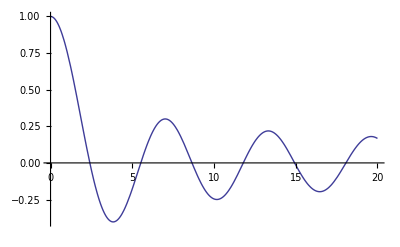

A second solution is singular as r→0 and two more modified functions are used when k is imaginary, a circumstance that can also be encountered.
Not surprisingly, Bessel functions also arise in cylindrical solutions to the wave equation.
Modified Bessel fiunctions figure prominently in the treatment of synchrotron radiation.

b) Problem is axisymmetric and so m=0. φ(r,z)→1 for r<1 as z→∞ so k real. 
Hence φ=1+A J_0(k r) e^(-k z)satisfies Laplace’s equation inside upper cylinder and φ(1,z>0)=1 if k is a zero of J_0.
More generally φ = 1 + ∑_i A_i J_0(k_i r) e^(-k_i z).
We also need φ(r<1,0)=0 ⇒A_i ∫_0^1 drrJ_0^2(k_i r) = 1/2 A_i J_1^2(k_i)=-∫_0^1 drrJ_0(k_i r) = (J_1(k_i))/k_i⇒A_i=-2/(k_i J_1(k_i)), and likewise for the lower cylinder

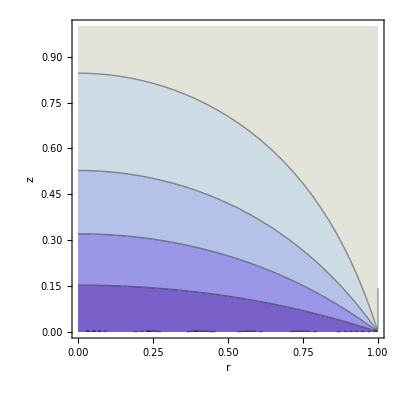

```mathematica
k=Table[N[BesselJZero[0,n]],{n,1,100}];φ=1-Sum[(2BesselJ [0,k[[n]] r] ⅇ^(-k[[n]]z))/(k[[n]] N[BesselJ[1,k[[n]]]]),{n,1,100}];
ContourPlot[φ,{r,0,1},{z,0,1},FrameLabel->{"r","z"},RotateLabel->False]
```

c) Solve the equation of motion for the electrons with initial conditions as z→-∞ u_r=0; (u·∇)u=-(q(1+u.u))^(1/2)/m∇φ, dr/dz=u_r/u_z wh ∇≡(∂_r,∂_z)
Observe that there will be focusing by the lower cylinder and (less) defocusing by the upper cylinder

Q2 Magneto-fluid-dynamics

a) The Maxwell stress tensor T is a three dimensional, second rank tensor that describes the stress associated with the electromagnetic field. Like all (normal) stress tensors it is symmetric and describes the force per unit are acting on the external world.

(Sometimes, it is helpful to think about this as a flux of momentum.) The forces act perpendicular and parallel to the surface. It can be expressed as the sum of an electric and a magnetic part each of which comprises an isotropic pressure ((ϵ_0 E^2)/2, B^2/(2 μ_0))  I and a tension (-ϵ_0 E⊗E, -(B⊗B)/μ_0). The form of T can be derived from the equating its divergence to the force density ρE+jxB using the Maxwell equations. An alternative approach is to regard T as a part of the special relativistic stress-energy tensor and express it in terms of products of the electromagnetic field 4-tensor F_αβ=∂_α A_β-∂_β A_α.
b) When k ⊥ B there is only magnetic pressure not tension. Flux-freezing implies that B ∝ ρ and so the magnetic pressure has P ∝ ρ^2. The wave is essentially a sound wave with γ=2 and the phase velocity is therefore B/(μ_0 ρ)^(1/2). Plasma pressure will add to the restoring force and increase the wave speed.
c) v ~ (3 x 10^-9)/((4 π 10^-7 x 10^-21)^(1/2))~100 km s^-1⇒Δt ~1.5 Ms ~ 17d.; Wave energy density U~10^(21-4)/(4π (1.5 x 10^11)^2 10^5) ~ 10^-11J m^-3⇒δB ~ (μ_0 U)^(1/2)~3 nT. The wave would be non-linear.
The wave will travel faster relative to the plasma on account of the thermal pressure and be convected by the plasma and so the travel time will be reduced to ~ a few days and the amplitude will be lower.

Q3 Cyclotron Radiation

a) As a transverse, vector wave, an electromagnetic wave can exhibit polarization.

Conventionally this is described by following the behavior of the oscillating electric field. If a single wave with a single frequency propagates in the z direction and the electric vector is directed along a single axis we call it linearly polarized; if the electric vector circles the z-axis we call it circularly polarized. If it is a mixture of these two case and the electric vector traces out an ellipse we call it elliptically polarized. Incoherent superpositions of waves can be partially polarized. It is then more useful to use the mean square electric field to measure the polarization. There are many conventions in use,  but a convenient one is use Stokes parameters 
I ~ < E_x^2 > + < E_y^2>,  Q ~  < E_x^2 > - < E_y^2>, U ~ <E_x E_y>, V~ <E_+^2>-<E_-^2> , where +,- refers to projections on 2^(-1/2)(x̂±i ŷ)
Waves propagating in media such as plasmas need not be transverse and can exhibit more complex polarization properties.
b) x along  Ωxn, y along nx(Ωxn), E ~ v_⊥ ~ [1, -i sinθ] where θ is the latitude. Hence C=(2sinθ)/(1+sin^2 θ). Note that it changes sign crossing the orbital plane.
When v~c the radiation is beamed on either side of the orbital plane and along the direction of motion. 
The two beams are strongly circularly polarized. but this will not be seen if they are combined in the detector.
c) p = eBR = 1eV/c ⇒ v~((3 x 10^8)^2)/(9.4 x 10^8)~100Mm s^-1; KE ~p^2/(2m)~50 MeV. dℰ/dt = v dp/dt = eBv dR/dt=-(μ_0 e^2 v^4)/(6 πcR^2) ⇒dR/dt~ 30 μ s^-1